# Exact Diagonalization of Schwinger [1803.03326]

```mathematica
(*fidelities from simulated noise --- if not recomputing *)
```

```mathematica
recomputeNoise = True;
```

## Settings: Lattice, Interpolating Operators, Model Parameters, and Truncation

Define the lattice

```mathematica
(*
    L = number of spatial sites;
    nfs = 2L, number of fermionic sites;
    fs[n] - wraps around the ends of the chain.
	
 Lattice is 0-indexed: 0, 1, ..., nfs - 1.
*)
ClearAll[L, nfs, fs, lattice]
L=2;                                                               
nfs =2 L;                                                      
fs[n_]:=Mod[n, nfs];                      
lattice = Table[fs[n], {n, 0, nfs-1}];
```

```mathematica
(* checks boundary conditions and the length of the chain *)
On[Assert];         
Assert[fs[nfs] == fs[0]];                  
Assert[fs[-1] == fs[nfs-1]];
Assert[Length[lattice] == nfs]     
Off[Assert]
```

Effective mass settings

```mathematica
srcInsertionSite = 1;  (* staggered lattice site on which the source form of the operator in inserted *)
srcInsertionSite2 = 1; (* in cases whern there is more than one operator term inserted --- CURRENTLY UNUSED *)
T =2* L;(* make rectangular lattice to mimick extraction of GS from Monte-Carlo *)
```

Define model parameters

```mathematica
ClearAll[pbc, a, g,w, J,m, m0, w0, J0, x, μ];
pbc = 1.0; (* 1.0 = periodic boundary conditions, -1.0 = antiperiodic*)
a = 1.;          (* lattice constant is fixed at 1*)
w0 = 1/(2a);    (* parameter for the kinetic term of the Hamiltonian *)
(* Relevant dimensionless parameters are with respect w0 *)
j0w0 =1.667; (* Note: these settings correspond to the ones in Martin's paper *)
m0w0 = 0.167;
w0t0 = 0.100; (* make smaller *)
(* the rest is determiHned... *)
J0 = j0w0 w0;
m0 = m0w0 w0 ; 
t0 = w0t0 / w0;
g = 2 √(J0 w0); 
params = {J-> J0, w-> w0, m->m0};
(* 
You can relate these settings to the parameters from Savage's paper:
*)
x =1/(a g)^2  (* x = 0.6 *)
μ = (2 m0)/(a g^2)  (* μ = 0.1 *)
```

0.59988

0.10018

```mathematica
w0t0
```

0.1

```mathematica
t0
```

0.2

Define truncation parameters

```mathematica
Λ1 =1;      (* primary cutoff - absolute value of each link should not exceed this; this restricts configs to those with winding number 0 *)
Λ2 = nfs; (* secondary cutoff - sum of squares of all links should not exceed this; setting it equal to nfs roughly corresponds to my QMC *)
Λ3 =Λ2 ;    (* secondary cutoff for the building the smart operator - determines the noisy small space over which optimization is performed *)
```

```mathematica
LTruncNoise=2;
```

```mathematica
Λ3Noise=3;
```

## Notebook Setup --- image resolution, output directory, etc.

```mathematica
ClearAll[imageRes];
imageRes = 250; (* image resolution for exporting images *)
```

```mathematica
ClearAll[dirName];
SetDirectory[NotebookDirectory[]]; (* by default, files are saved in the same directory as the notebook *)
dirName = ToString[StringForm["data_L`1`", L]];
If[!DirectoryQ[dirName],CreateDirectory[dirName]];
```

```mathematica
conventionFileName[s_String, L_Integer, Λ1_Integer, Λ2_Integer, extension_String]:=ToString[StringForm["`1`/`2`_L`3`_lmd1_`4`_lmd2_`5`.`6`", dirName,s,L, Λ1,Λ2, extension]];
```

```mathematica
(* stops non-essential cells that scale badly from running for all but small chains, prevent large printouts *)
ClearAll[excludeSlow, verbose];
excludeSlow = L≥6;
verbose = L ≤6;
```

```mathematica
(* True if want to use variational data from smaller-volume system to construct improved operators for a larger-volume system. In that case, must specify filenames where the coefficients for O1 and O2 expansion are stored *)
ClearAll[useDiffCoeffs,op1CoeffsName,op2CoeffsName];
useDiffCoeffs=False;
op1CoeffsName = "o1Coeffs";
op2CoeffsName = "o2Coeffs";
```

## Define rules, the Hamiltonian, and construct a basis

Define all operators and rules (aggregated from all sections)

## Basics and Normalization

```mathematica
ClearAll[basics, normalization]
basics = {
before___.(n_ b_).after___/;NumericQ[n]:> n before.b.after,
before___.(a_+b_).after___:> before.a.after+before.b.after,
a___ +0.+b___ :>a+b,
Dot[x_,0]:>0};
normalization={
(* all kets are normalized *)
psi1_Ket.psi2_Ket :> Boole[List[Delete[0]@psi1]==List[Delete[0]@psi2]],
0.`.psi_Ket :> 0};
```

## Operators in the Hamiltonian

```mathematica
ClearAll[operators]
operators={Dot[anything_,0]->0,             (* needed to have something like Subscript[σ, z][1].Subscript[σ, z][1].Ket[0]] :> 0 *)
a___ +0.+b___ :>a+b,
Subscript[σ, z][n_].psi_Ket:>psi[[n + 1]]psi,
Subscript[σ, z][n_].(x_ psi_Ket):>x Subscript[σ, z][n].psi/;NumericQ[x],
SubPlus[σ][n_].psi_Ket :>If[psi[[n + 1]] == 1,0,ReplacePart[psi, n + 1->psi[[n+ 1]] + 2]],
SubPlus[σ][n_].(x_ psi_Ket):>x SubPlus[σ][n].psi/;NumericQ[x],
SubMinus[σ][n_].psi_Ket :>If[psi[[n + 1]] == -1,0,ReplacePart[psi, n+ 1->psi[[n + 1]]-2]],
SubMinus[σ][n_].(x_ psi_Ket):>x SubMinus[σ][n].psi/;NumericQ[x],
SubMinus[U][n_].psi_Ket :> If[psi[[n+nfs+ 1]] == -Λ1,0,ReplacePart[psi, n+nfs + 1->psi[[n + nfs + 1]]-1]],
SubMinus[U][n_].(x_ psi_Ket):>x SubMinus[U][n].psi/;NumericQ[x],
SubPlus[U][n_].psi_Ket :> If[psi[[n+nfs+ 1]] == Λ1,0,ReplacePart[psi, n+nfs + 1->psi[[n + nfs + 1]]+1]],
SubPlus[U][n_].(x_ psi_Ket):>x SubPlus[U][n].psi/;NumericQ[x],
l[n_].psi_Ket:>psi[[n +nfs+ 1]]psi,
l[n_].(x_ psi_Ket):>x l[n].psi/;NumericQ[x]};
```

Null

```mathematica
density ={
SubPlus[χ][i_].psi_Ket :>If[psi[[i + 1]] == 1,0,ReplacePart[psi, i + 1->psi[[i+ 1]] + 1]],
SubPlus[χ][i_].(x_ psi_Ket):>x SubPlus[χ][i].psi/;NumericQ[x],
SubMinus[χ][i_].psi_Ket :>If[psi[[i + 1]] == 0,0,ReplacePart[psi, i+ 1->psi[[i + 1]]-1]],
SubMinus[χ][i_].(x_ psi_Ket):>x SubMinus[χ][i].psi/;NumericQ[x]};
```

### Null

```mathematica
(* helper functions to determine the direction of hopping on a lattice with PBC *)
ClearAll[indexDiff, isLeft, isRight, hop];
(* 
given two integers a and b and a 0/1 checkLeft, 
checks if jumping FROM a TO b corresponds hopping 
	- to the LEFT by 1 site if checkLeft is 1
	- to the RIGHT by 1 site if checkLeft is 0
*)
indexDiff[a_, b_, checkLeft_]/; checkLeft == 1 ∨ checkLeft ==0:=If[Quotient[b-a, nfs] ≥0,Mod[b-a, nfs]==(-1)^checkLeft, (b-a)-(Quotient[b-a, nfs]+1)*nfs == (-1)^checkLeft];
(* checks hopping LEFT *)
(* when indices are not yet specified *)
isLeft[i_ +a_Integer, i_+b_Integer]/;fs[Abs[b-a]]==1:=indexDiff[a, b, 1];
isLeft[i_, i_+a_Integer]/;fs[Abs[a]]==1:=indexDiff[0, a, 1];
isLeft[i_+a_Integer, i_]/;fs[Abs[a]]==1:=indexDiff[a, 0, 1];
(* when indices are specified *)
isLeft[i_Integer, j_Integer]/; Min[fs[i-j], nfs - fs[i-j]]==1:=(i-j)==1 ∨(i==0 ∧ j == nfs-1);
(* checks hopping RIGHT *)
(* when indices are not yet specified *)
isRight[i_ +a_Integer, i_+b_Integer]/;fs[Abs[b-a]]==1:=indexDiff[a, b, 0];
isRight[i_, i_+a_Integer]/;fs[Abs[a]]==1:=indexDiff[0, a, 0];
isRight[i_+a_Integer, i_]/;fs[Abs[a]]==1:=indexDiff[a, 0, 0];
(* when indices are specified *)
isRight[i_Integer, j_Integer]/; Min[fs[i-j], nfs - fs[i-j]]==1:=(i-j)==-1 ∨(i==nfs-1 ∧ j == 0);
ClearAll[hop]
hop[i_, j_ ]/; Min[fs[i-j], nfs - fs[i-j]]==1 := If[isLeft[i, j],SubPlus[χ][fs[j]].SubPlus[U][fs[j]].SubMinus[χ][fs[i]], SubPlus[χ][fs[j]].SubMinus[U][fs[i]].SubMinus[χ][fs[i]]];
```

```mathematica
(* Substituting this rule will change all α's for the function hop  *)
ClearAll[hoppingReplacement];
hoppingReplacement = {α-> hop};
```

## Translation Operator

```mathematica
ClearAll[translation]
translation = {
(* break into spins and links, and shift each separately by an integer number of spatial sites *)
T[n_].psi_Ket:> Flatten[RotateRight[Partition[psi, nfs], {0,Mod[2 n, nfs]}]],
T[n_].(x_ psi_Ket):>x T[n].psi/;NumericQ[x]};
```

## Parity Operator

```mathematica
ClearAll[parity]
parity = {
(* this permutation fixes points 0 and nfs/2 on the lattice and reflects points along the axis through these points; links are permuted and reversed; fixing any other pair of diametric points yields the same states *)
P.psi_Ket:> Ket @@ MapThread[
Times,
(* remove Ket from the head to perform normal list operations *)
{List[Delete[0]@
Permute[psi, 
Cycles[Join[
(* these permutations reflect lattice points across the axis through sites 0 and nfs/2*)
Table[{n+1,nfs-n +1},{n, 1, nfs/2-1}],
(* these permutations reflect links across the axis through sites 0 and nfs/2; directions are not flipped yet *)
Table[{n+1 + nfs,nfs-n + nfs}, {n, 0,nfs/2-1}]]]]],
(* flip directions on all of the links once everything is permuted *)
Join[ones, -ones]/.ones ->Table[1,{i, nfs}]}] ,
P.(x_ psi_Ket):>x P.psi/;NumericQ[x]};
```

## Operator to convert spins to fermions

```mathematica
ClearAll[spinMap]
spinMap = {
(* sends the ket of spins + links to a ket of fermions + links *)
		
S.psi_Ket:> Ket @@ (* apply ket again *)
(Flatten[(Partition[List[ (* parition the list into a list of spins and a list of kets*)
(* delete the ket head to split the list into spins and kets *)
Delete[0]@psi], 
	(* spins are converted to fermions, links are untouched *)
nfs]+{1, 0})*{1/2,1}]) ,
S.(x_ psi_Ket):>x S.psi/;NumericQ[x]};
```

## Operator to convert fermions to spins

```mathematica
ClearAll[fermionMap]
fermionMap = {
(* sends the ket of spins + links to a ket of fermions + links *)
		
F.psi_Ket:> Ket @@ (* apply ket again *)
(Flatten[(Partition[List[ (* parition the list into a list of spins and a list of kets*)
(* delete the ket head to split the list into spins and kets *)
Delete[0]@psi], 
	(* fermions are converted to spins, links are untouched *)
nfs]*{2, 1})-{1,0}]) ,
F.(x_ psi_Ket):>x F.psi/;NumericQ[x]};
```

## Projection

```mathematica
killsGS = {
(* kills the ket if the link is not zero *)	
δl[i_].psi_Ket:> If[psi⟦nfs+1 + i⟧ ==0, psi,0],
δl[i_].(x_ psi_Ket):>x δl[i].psi/;NumericQ[x]};
projectionReplacement={Π.psi_Ket :>Apply[Dot,Table[δl[fs[i]], {i, 0, nfs-1}]].psi,
Π.(x_ psi_Ket):>x Π.psi/;NumericQ[x]};
```

## Aggregate all the rules

```mathematica
rules =Join[basics,normalization, translation, parity,operators, spinMap,fermionMap,hoppingReplacement, density, killsGS,projectionReplacement];
```

Define the Hamiltonian

```mathematica
ClearAll[Hhop, Hmass, Hfield,H]
```

## Hopping terms

```mathematica
Hhop = Sum[w SubPlus[σ][fs[n]].SubPlus[U][fs[n]].SubMinus[σ][fs[n+1]].Ket[Ψ] +w SubPlus[σ][fs[n+1]].SubMinus[U][fs[n]].SubMinus[σ][fs[n]].Ket[Ψ] ,{n,0, nfs-2}]+pbc*w SubPlus[σ][fs[nfs-1]].SubPlus[U][fs[nfs-1]].SubMinus[σ][fs[nfs]].Ket[Ψ] +pbc *w SubPlus[σ][fs[nfs]].SubMinus[U][fs[nfs-1]].SubMinus[σ][fs[nfs-1]].Ket[Ψ] ;
HoldForm[Sum[w SubPlus[σ][fs[n]].SubPlus[U][fs[n]].SubMinus[σ][fs[n+1]].Ket[Ψ] +w SubPlus[σ][fs[n+1]].SubMinus[U][fs[n]].SubMinus[σ][fs[n]].Ket[Ψ] ,{n,0, nfs-2}] + pbc*(w SubPlus[σ][fs[nfs-1]].SubPlus[U][fs[nfs-1]].SubMinus[σ][fs[nfs]].Ket[Ψ] +pbc*w SubPlus[σ][fs[nfs]].SubMinus[U][fs[nfs-1]].SubMinus[σ][fs[nfs-1]].Ket[Ψ]) ;]
```

∑_(n=0)^(nfs-2) (w σ_+[fs[n]].U_+[fs[n]].σ_-[fs[n+1]].Ψ+w σ_+[fs[n+1]].U_-[fs[n]].σ_-[fs[n]].Ψ)+pbc (w σ_+[fs[nfs-1]].U_+[fs[nfs-1]].σ_-[fs[nfs]].Ψ+pbc w σ_+[fs[nfs]].U_-[fs[nfs-1]].σ_-[fs[nfs-1]].Ψ);

## Mass Terms

```mathematica
Hmass = Sum[m/2(-1)^n Subscript[σ, z][fs[n]].Ket[Ψ],{n,0, nfs-1}] ;
HoldForm[ Sum[m/2(-1)^n Subscript[σ, z][fs[n]].Ket[Ψ],{n,0, nfs-1}] ]
```

∑_(n=0)^(nfs-1) 1/2 m (-1)^n σ_z[fs[n]].Ψ

## Electric Field Flux Terms

```mathematica
Hfield = Sum[J l[fs[n]].l[fs[n]].Ket[Ψ],{n,0, nfs-1}] ;
HoldForm[Sum[J l[fs[n]].l[fs[n]].Ket[Ψ],{n,0, nfs-1}]]
```

∑_(n=0)^(nfs-1) J l[fs[n]].l[fs[n]].Ψ

## Total Hamiltonian

```mathematica
H =  Simplify[Hhop + Hmass + Hfield];
```

Define the VQS Basis

## Generate all allowed spin configurations (total spin = 0)

```mathematica
ClearAll[spinKets];
Block[{singleSpinBasis, singleLinkBasis},
singleSpinBasis = {1,-1}; 
spinKets = Ket @@@ Select[Tuples[singleSpinBasis, nfs], Total[#]== 0 &];
];
```

## Form all kets allowed by Gauss’s law

### Define functions that generate the states

```mathematica
ClearAll[gaussLaw, getGaussBasis];
gaussLaw[site_]:=l[fs[site]] - l[fs[site-1]] - 1/2(s[fs[site]] + (-1)^site) ==0; 
(* 
This method generates all possible configurations of links and then pattern-matches them according to Gauss's law. It's memory-intensive, don't use for more than L = 4 spatial sites.
*)
getGaussBasis[L_Integer]/;1≤L≤4:=Block[{singleLinkBasis, linkKets},
singleLinkBasis = Table[l, {l, -Λ1, Λ1}];
(*impose second cutoff on the sum of the squares of the links*)
linkKets =Ket @@@ Select[Tuples[singleLinkBasis, nfs], Total[#^2] ≤ Λ2 &];(* choose subspace with Q = 0 *)
basisGauss= Flatten @ 
Parallelize[Outer [
If[(* for all n, | L[n] - L[n-1] - 1/2(Subscript[σ, z][n] + (-1)^n) | must be 0 *)
AllTrue[Range[0, nfs-1], Function[n,Abs[#2⟦fs[n]+1⟧ - #2⟦fs[n-1]+1⟧ - 1/2(#1⟦fs[n]+1⟧ + (-1)^n) ]==0]],
Join[#1,#2],Nothing] &, 
spinKets, linkKets]]];
(*
This method solves for all links configurations compatible with each spin configuration. Less memory-intensive, but solving is more expensive than pattern-matching. Use of more than L=4 spatial sites.
*)
getGaussBasis[L_Integer]/;L > 4:=Block[{$RecursionLimit=∞,links, constr1, constr2, constr,allowedLinks, linkKets, ctr},
links = Table[l[site], {site, 0, nfs -1}];
constr1 = Table[Abs[l[site]]≤Λ1, {site, 0, nfs-1}];
constr2 = {links.links ≤ Λ2};
constr = Join[constr1, constr2];
allowedLinks[spinKet_]:=Block[{s, eqs, sols},
s[site_Integer]:=spinKet⟦site+1⟧ ;(* shift by one for Mathematica's list indexing *)
eqs = Table[gaussLaw[site], {site, 0, 
nfs-1}];
sols = Solve[Join[eqs, constr], links, Integers];
If[Length[sols] ==0,{},Ket @@links/.sols]];
ctr = 0; 
SetSharedVariable[ctr];
Monitor[linkKets=
ParallelTable[ctr++;allowedLinks[spinKets⟦i⟧],{i, 1, Length[spinKets]}],
Row[{ProgressIndicator[ctr,{1,Length[spinKets]}],ctr, "/", Length[spinKets]}, " "]];
basisGauss = Flatten @ ParallelTable[If[Length[#]==0,Nothing,Join[spinKets⟦i⟧, #]]&/@linkKets⟦i⟧, {i,1,Length[spinKets]}];
Return[basisGauss];
];
```

### Load the basis if it already exists; compute otherwise

```mathematica
gaussBasisFileName[L_Integer, Λ1_Integer, Λ2_Integer]:=conventionFileName["basisGauss", L, Λ1, Λ2, "txt"];
```

```mathematica
ClearAll[basisGauss];
basisGauss = If[FileExistsQ[gaussBasisFileName[L, Λ1, nfs]],
(* If file exists, load it *)
Ket@Delete[0]@#&/@Import[gaussBasisFileName[L, Λ1, nfs], "Table"],
(* Else, compute it *)
getGaussBasis[L]];
If[!FileExistsQ[gaussBasisFileName[L, Λ1, nfs]], Export[gaussBasisFileName[L, Λ1, nfs], List@Delete[0]@#&/@basisGauss, "Table"]]
StringForm["Gauss basis has `1` elements", Length[basisGauss]];
```

data_L2/basisGauss_L2_lmd1_1_lmd2_4.txt

### Truncate on Flux

```mathematica
basisGauss=SortBy[basisGauss, ((1/J) * Hfield/.Ket[Ψ]->#/.params//.rules).# //.rules&];
basisGauss=Select[basisGauss,Round[((1/J) * Hfield/.Ket[Ψ]->#/.params//.rules).# //.rules] ≤Λ2 &];
```

#### Size of Gauss basis

```mathematica
Length[basisGauss]
```

13

#### Size of Gauss basis, if links are integrated out and only spins are left ( this is what Christine would use)

```mathematica
Length[spinKets]
```

6

## Get the zero momentum sector

```mathematica
ClearAll[getKSector, k0Sector];
getKSector[k_Integer]:=DeleteDuplicates[Table[Simplify[sum/Sqrt[sum.sum]/.sum-> Sum[T[n].basisKet Exp[ⅈ 2π k/L], {n, 0, L-1}] //. rules],{basisKet,basisGauss}]];
k0Sector= getKSector[0];
StringForm["Zero-Momentum Sector has `1` basis kets", Length[k0Sector]]
```

Zero-Momentum Sector has 9 basis kets

## Within the zero momentum sector, form states of good parity --- this is what Martin would use

```mathematica
ClearAll[getPSector, evenPSectorUnsorted, oddPSectorUnsorted];
getPSector[n_Integer, k0Sector_] := 
DeleteDuplicatesBy[DeleteCases[
(* delete any repeated states as defined below *)
ParallelTable[Expand[PAIRity/(Sqrt[PAIRity.PAIRity])/.PAIRity
(* add or subtract parity-transformed state to get one of the sectors *)
->Simplify[(kVec +(-1)^n (P.kVec//. rules))//.rules]//.rules],{kVec,k0Sector}],
(* delete any zeroes *)
0],
(* delete any states that are the same / same up to a sign *)
(* this version is faster than pairwise comparison! *)
Sort[{#,(-1)^n#}]&];
evenPSectorUnsorted = getPSector[0, k0Sector];
oddPSectorUnsorted = getPSector[1, k0Sector];
StringForm["Even-parity sector has `1` basis kets", Length[evenPSectorUnsorted]]
StringForm["Odd-parity sector has `1` basis kets", Length[oddPSectorUnsorted]]
```

Even-parity sector has 5 basis kets

Odd-parity sector has 4 basis kets

## Pre-sort the bases in the ascending order of electric flux

```mathematica
evenPSectorPresorted=SortBy[evenPSectorUnsorted, ((1/J) * Hfield/.Ket[Ψ]->#/.params//.rules).# //.rules&];
oddPSectorPresorted=SortBy[oddPSectorUnsorted, ((1/J) * Hfield/.Ket[Ψ]->#/.params//.rules).# //.rules &];
```

## Define functions for sorting the states in variational basis

Mathematica does not keep a consistent ordering of states in the basis at different volumes (it treats kets as some alphanumeric lists). I want to force a particular ordering for easier comparison. Below, improved interpolating operators refer to constructions we used prior to link fields: each term takes the bare vacuum state into some other ket. I use these terms to order the states in the variational basis with each flux sector

#### Normalization factor

```mathematica
(* 
	I would like to write the terms of the improved operator in the local ("source") form,
that can then be summed to get the zero-momentum ("sink") form over the whole lattice

Some local forms span several spatial lattice sites. If that local patch is big compared to lattice size, summing it over may lead to overcounting. This normalization factor accounts for it. 
*)
norm[i_Integer]/; i≥1 :=1/(√If[L/i==2,2, 1]);
```

#### The Bare Vacuum State

```mathematica
(* Here I use the kets converted to the fermion language *)
bareVac =Ket@@Join[Table[Boole[Mod[i, 2] == 0], {i,1, nfs}], ConstantArray[0, nfs]]
```

0,1,0,1,0,0,0,0

#### Variational Basis for the Even-Parity Sector, To Be Sorted --- Converted to Fermions

```mathematica
Block[{evenPSectorTable},
evenPSectorTable = SortBy[
ParallelTable[
{(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->evenPSectorPresorted⟦i⟧/.params//.rules].evenPSectorPresorted⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.evenPSectorPresorted[[i]]//. rules}, {i, Length[evenPSectorPresorted]}],
Abs[#⟦1⟧] &]; 
If[verbose,Print[evenPSectorTable//TableForm]];
varBasis1Presorted = evenPSectorTable⟦All,2⟧;
];
(* Mathematica does not keep the ordering of the states consistently at different volumes; for easier comparison at diferent volumes, I will force a particular ordering *)
```

0 | 0,1,0,1,0,0,0,0
1. | 1/2 0,0,1,1,0,-1,0,0+1/2 0,1,1,0,0,0,1,0+1/2 1,0,0,1,1,0,0,0+1/2 1,1,0,0,0,0,0,-1
2. | (1,0,1,0,0,-1,0,-1)/(√2)+(1,0,1,0,1,0,1,0)/(√2)
3. | 1/2 0,0,1,1,1,0,1,1+1/2 0,1,1,0,-1,-1,0,-1+1/2 1,0,0,1,0,-1,-1,-1+1/2 1,1,0,0,1,1,1,0
4. | (0,1,0,1,-1,-1,-1,-1)/(√2)+(0,1,0,1,1,1,1,1)/(√2)

#### Variational Basis for the Odd-Parity Sector, To Be Sorted --- Converted to Fermions

```mathematica
Block[{oddPSectorTable},
oddPSectorTable = SortBy[
ParallelTable[
{(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->oddPSectorPresorted⟦i⟧/.params//.rules].oddPSectorPresorted⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.oddPSectorPresorted[[i]]//. rules}, {i, Length[oddPSectorPresorted]}],
Abs[#⟦1⟧] &]; 
If[verbose,Print[oddPSectorTable//TableForm]];
varBasis2Presorted = oddPSectorTable⟦All,2⟧
];
(* Mathematica does not keep the ordering of the states consistently at different volumes; for easier comparison at diferent volumes, I will force a particular ordering *)
```

1. | 1/2 0,0,1,1,0,-1,0,0-1/2 0,1,1,0,0,0,1,0-1/2 1,0,0,1,1,0,0,0+1/2 1,1,0,0,0,0,0,-1
2. | (1,0,1,0,0,-1,0,-1)/(√2)-(1,0,1,0,1,0,1,0)/(√2)
3. | 1/2 0,0,1,1,1,0,1,1-1/2 0,1,1,0,-1,-1,0,-1-1/2 1,0,0,1,0,-1,-1,-1+1/2 1,1,0,0,1,1,1,0
4. | (0,1,0,1,-1,-1,-1,-1)/(√2)-(0,1,0,1,1,1,1,1)/(√2)

#### Sorting the predefined terms into their flux sectors

```mathematica
defOpFluxSectors[flux_Integer, indices_List, opFluxSec_List, op_List]:=
Module[{f = flux},
opFluxSec⟦1⟧[f]=Table[op⟦1⟧[index], {index,indices}];(* source form *)
opFluxSec⟦2⟧[f]=Table[op⟦2⟧[index], {index,indices}]; (* dagger of source form *)
opFluxSec⟦3⟧[f]=Table[op⟦3⟧[index], {index,indices}]; (* sink form *)
opFluxSec⟦4⟧[f]=Table[op⟦4⟧[index], {index,indices}](* dagger of sink form *) ; 
];
```

#### Separating the variational basis into flux sectors

```mathematica
(*
Get fluxSectors: a list of lists, where each sublist contains the basis kets whose links satisfy the global cutoff of Λ2. The first list contains flux-0 kets, then flux-1 kets, and so on.
*)
getFluxSectors[paritySector_]:= 
Block[{paritySectorTable, fluxSectorsList,fluxes},
paritySectorTable = SortBy[
ParallelTable[
{(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->paritySector⟦i⟧/.params//.rules].paritySector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.paritySector[[i]]//. rules}, {i, Length[paritySector]}],
Abs[#⟦1⟧] &]; 
fluxSectorsList= Split[paritySectorTable,#1⟦1⟧==#2⟦1⟧ &];
(* list of fluxes corresponding to non-empty flux sectors *)
fluxes=DeleteDuplicates[
Round[Flatten[
Function[fluxSector, 
Flatten[Map[Take[#, 1] &, fluxSector]]]
/@fluxSectorsList]]];
fluxSectorsList=Function[fluxSector, Flatten[Map[Drop[#, 1] &, fluxSector]]]/@fluxSectorsList;
fluxSectorsList=MapThread[Function[{flux, fluxSector},{flux, fluxSector}],{fluxes, fluxSectorsList}];
For[flux = 0, flux ≤ Λ2, flux++1, 
fluxSectorFunc[flux]=If[Length[#]==0, #, Simplify[First[#]⟦2⟧]] & @ Select[fluxSectorsList,Round[#⟦1⟧]==flux&]];
];
```

#### Sorting within each flux sector according to the terms of the quantum-improved operators

```mathematica
(* 

  I want to define a particular ordering of states in my variational basis.

Within each flux sector, the first kets are those corresponding to the terms of the improved operators in that sector, in the order defined by lists op1FluxIndices[flux]
	
For each flux sector, I build a table of these position indices from applying operators from the variational bases in order; then, in that order, pull those indices to the front of each list.

*)
buildSortingList[flux_Integer,opDagSnkFluxSec_, fluxSector_]:=Block[{innerProds},
innerProds= Table[
(* This applies a smart operator term to each ket in the flux sector, for each operator term *)
Map[Expand[(opDagSnkFluxSec[flux]⟦opIndex⟧/.state-> # //.rules ).bareVac//.rules &], fluxSector[flux]],
{opIndex, 1, Length[opDagSnkFluxSec[flux]]}];
indexOrdering[flux]=Table[
(* This finds the position of the ket which, when acted on by a smart operator term, yields inner product 1 with the bare vacuum *)
Flatten[Position[innerProds⟦opIndex⟧, 1,1]], 
{opIndex, 1, Length[opDagSnkFluxSec[flux]]}];
];
```

```mathematica
(* Given the list of indices corresponding to the kets to be pulled at the beginning of the flux sector list, this function does exactly that *) 
sortFluxSector[flux_Integer, fluxSector_, indexOrdering_]:=
Block[{shuffledKets, istart}, 
(* save the elements to be pulled at the beginning of the list in a separate variable *)
ketsToShuffle=Flatten[Table[fluxSector[flux]⟦index⟧, {index, indexOrdering[flux]}]];
(* Print abosolute ordering *)
istart = Sum[Length[fluxSector[iflux]],{iflux, 0,flux-1 }];
Print[{flux, istart + Flatten[indexOrdering[flux]]}];
(* delete those elements from the original list *)
If[Length[Flatten[ketsToShuffle]] > 0,
(* if some kets need to be shuffled ... *)
(* delete those elements from the original list *)
fluxSectorSorted[flux]=Delete[fluxSector[flux], indexOrdering[flux]//.{}->Sequence[]];
(* reverse the saved list of kets to be shuffled, so that the ket that will be first is last in the list *)
ketsToShuffle = Reverse[ketsToShuffle];
(* prepend all the saved kets to the flux sector list with deleted elements *)
For[iket =1,iket≤Length[ketsToShuffle],iket++, 
PrependTo[fluxSectorSorted[flux],ketsToShuffle⟦iket⟧]],
(* otherwise no kets need to be shuffled ... *)
fluxSectorSorted[flux]=fluxSector[flux]];
];
```

## Operator 1: BareVac ⇒ π = +1 state

### 1

```mathematica
(* ground state stays in the ground state*)
```

```mathematica
gsOpSrc[1][i_]:=1/L state;
gsOpDagSrc[1][i_]:=1/L state;
gsOpSnk[1] = Sum[gsOpSrc[1][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[1] = Sum[gsOpDagSrc[1][i],{i, 1, nfs-1, 2}];
```

### 2

```mathematica
(* 1 hop, summed over all spatial sites *)
```

```mathematica
gsOpSrc[2][i_]:=1/(√(2L))(α[fs[i],fs[i-1]].state+α[fs[i], fs[i+1]].state);
gsOpDagSrc[2][i_]:=1/(√(2L))(α[fs[i-1],fs[i]].state+α[fs[i+1], fs[i]].state);
gsOpSnk[2] = Sum[gsOpSrc[2][i],{i, 1, nfs-1, 2}];
(* sum over all even sites to get the inverse  *)
gsOpDagSnk[2] = Sum[gsOpDagSrc[2][i],{i, 1, nfs-1, 2}];
```

### 3

```mathematica
(* simultaneous hopping on two neighboring  spatial sites in the same direction *)
gsOpSrc[3][i_]:=norm[1] 1/(√(2 L))(α[fs[i],fs[i+1]].α[fs[i+2],fs[i+3]].state+α[fs[i-2], fs[i-3]].α[fs[i], fs[i-1]].state);
gsOpDagSrc[3][i_]:=norm[1] 1/(√(2 L))(α[fs[i+3],fs[i+2]].α[fs[i+1],fs[i]].state+α[fs[i-1], fs[i]].α[fs[i-3], fs[i-2]].state);
gsOpSnk[3]:=Sum[gsOpSrc[3][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[3] = Sum[gsOpDagSrc[3][i],{i, 1, nfs-1, 2}];
```

### 4

```mathematica
(* 
simultaneous hopping on two spatial sites in the same direction, separated by a spatial site, summed over all spatial sites 
factor of norm because each term is counted twice with L = 4, to avoid overcounting the pairs. however this is only a problem for L = 4.
*)
gsOpSrc[4][i_]:=norm[2] 1/(√(2L))(α[fs[i], fs[i+1]].α[fs[i+4], fs[i+5]].state+α[fs[i],fs[i-1]].α[fs[i-4],fs[i-5]].state);
gsOpDagSrc[4][i_]:=norm[2] 1/(√(2L))(α[fs[i+5], fs[i+4]].α[fs[i+1], fs[i]].state+α[fs[i-5],fs[i-4]].α[fs[i-1],fs[i]].state);
gsOpSnk[4]:=Sum[gsOpSrc[4][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[4] = Sum[gsOpDagSrc[4][i],{i, 1, nfs-1, 2}];
```

### 5

```mathematica
(* 
simultaneous hopping on two neighboring spatial sites, in opposite directions, "away from each other", summed over all spatial sites 
*)
gsOpSrc[5][i_]:=1/(√L)(α[fs[i],fs[i-1]].α[fs[i+2],fs[i+3]].state);
gsOpDagSrc[5][i_]:=1/(√L)(α[fs[i+3],fs[i+2]].α[fs[i-1],fs[i]].state);
gsOpSnk[5]:=Sum[gsOpSrc[5][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[5] = Sum[gsOpDagSrc[5][i],{i, 1, nfs-1, 2}];
```

### 6

```mathematica
(* 
simultaneous hopping on two neighboring even sites, separated by a spatial site, "toward each other", summed over all spatial sites 
*)
gsOpSrc[6][i_]:=1/(√L)(α[fs[i],fs[i+1]].α[fs[i+4],fs[i+3]].state);
gsOpDagSrc[6][i_]:=1/(√L)(α[fs[i+3],fs[i+4]].α[fs[i+1],fs[i]].state);
gsOpSnk[6]:=Sum[gsOpSrc[6][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[6] = Sum[gsOpDagSrc[6][i],{i, 1, nfs-1, 2}];
```

### 7

```mathematica
(* 
simultaneous hopping on two spatial sites in the same direction, separated by 2 spatial sites, summed over all spatial sites 
factor of norm because each term is counted twice with L = 4, to avoid overcounting the pairs. however this is only a problem for L = 4.
*)
gsOpSrc[7][i_]:=norm[3] 1/(√(2 L))(α[fs[i],fs[i+1]].α[fs[i+6],fs[i+7]].state+α[fs[i-6], fs[i-7]].α[fs[i], fs[i-1]].state);
gsOpDagSrc[7][i_]:=norm[3] 1/(√(2 L))(α[fs[i+7],fs[i+6]].α[fs[i+1],fs[i]].state+α[fs[i-1], fs[i]].α[fs[i-7], fs[i-6]].state);
gsOpSnk[7]:=Sum[gsOpSrc[7][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[7] = Sum[gsOpDagSrc[7][i],{i, 1, nfs-1, 2}];
```

### 8

```mathematica
(* 
simultaneous hopping on two spatial sites, separated by a spatial site, in opposite directions, "away from each other", summed over all spatial sites 
*)
gsOpSrc[8][i_]:=1/(√L)(α[fs[i],fs[i-1]].α[fs[i+4],fs[i+5]].state);
gsOpDagSrc[8][i_]:=1/(√L)(α[fs[i+5],fs[i+4]].α[fs[i-1],fs[i]].state);
gsOpSnk[8]:=Sum[gsOpSrc[8][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[8] = Sum[gsOpDagSrc[8][i],{i, 1, nfs-1, 2}];
```

### 9

```mathematica
(* 
simultaneous hopping on two spatial sites, separated by 2 spatial sites, "toward each other", summed over all spatial sites.
*)
gsOpSrc[9][i_]:=1/(√L)(α[fs[i],fs[i+1]].α[fs[i+6],fs[i+5]].state);
gsOpDagSrc[9][i_]:=1/(√L)(α[fs[i+5],fs[i+6]].α[fs[i+1],fs[i]].state);
gsOpSnk[9]:=Sum[gsOpSrc[9][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[9] = Sum[gsOpDagSrc[9][i],{i, 1, nfs-1, 2}];
```

### 10

```mathematica
(* 
simultaneous hopping on 3 adjacent spatial sites in the same direction, summed over all spatial sites 
*)
```

```mathematica
gsOpSrc[10][i_]:=1/(√(2 L))(α[fs[i], fs[i+1]].α[fs[i+2], fs[i+3]].α[fs[i+4], fs[i+5]].state+α[fs[i], fs[i-1]].α[fs[i-2], fs[i-3]].α[fs[i-4], fs[i-5]].state);
gsOpDagSrc[10][i_]:=1/(√(2 L))(α[fs[i+5], fs[i+4]].α[fs[i+3], fs[i+2]].α[fs[i+1], fs[i]].state+α[fs[i-5], fs[i-4]].α[fs[i-3], fs[i-2]].α[fs[i-1], fs[i]].state);
gsOpSnk[10]:=Sum[gsOpSrc[10][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[10] = Sum[gsOpDagSrc[10][i],{i, 1, nfs-1, 2}];
```

### 11

```mathematica
(* 

SMALL WEIGHT. This particular state would be hard to realize in Monte-Carlo.

simultaneous hopping of on two neighboring even sites in the same direction; on of the fermions jumps twice so they end on neighboring (fermionic) sites; summed over all spatial sites 

*)
gsOpSrc[11][i_]:=1/(√(2L))(α[fs[i-1], fs[i]].α[fs[i-2], fs[i-1]].α[fs[i], fs[i+1]].state + α[fs[i+1], fs[i]].α[fs[i+2], fs[i+1]].α[fs[i], fs[i-1]].state);
gsOpDagSrc[11][i_]:=1/(√(2L))(α[fs[i+1], fs[i]].α[fs[i-1], fs[i-2]].α[fs[i], fs[i-1]].state + α[fs[i-1], fs[i]].α[fs[i+1], fs[i+2]].α[fs[i], fs[i+1]].state);
gsOpSnk[11]:=Sum[gsOpSrc[11][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[11] = Sum[gsOpDagSrc[11][i],{i, 1, nfs-1, 2}];
```

### 12

```mathematica
(* simultaneous hopping on two adjacent spatial sites in the same direction; and in the opposite direction from the spatial site that is next to nearest to one of the two adjacent sites *)
gsOpSrc[12][i_]:=1/(√(2 L))(α[fs[i],fs[i+1]].α[fs[i+2],fs[i+3]].α[fs[i+6],fs[i+5]].state 
+α[fs[i],fs[i+1]].α[fs[i+4],fs[i+3]].α[fs[i+6],fs[i+5]].state);
gsOpDagSrc[12][i_]:=1/(√(2 L))(α[fs[i+5],fs[i+6]].α[fs[i+3],fs[i+2]].α[fs[i+1],fs[i]].state 
+ α[fs[i+5],fs[i+6]].α[fs[i+3],fs[i+4]].α[fs[i+1],fs[i]].state);
gsOpSnk[12]:=Sum[gsOpSrc[12][i],{i, 1, nfs-1, 2}];
gsOpDagSnk[12] = Sum[gsOpDagSrc[12][i],{i, 1, nfs-1, 2}];
```

### Order operators within each flux sector

```mathematica
ClearAll[op1SrcFluxSec, op1DagSrcFluxSec,op1SnkFluxSec, op1DagSnkFluxSec];
op1FluxSec={op1SrcFluxSec, op1DagSrcFluxSec,op1SnkFluxSec,op1DagSnkFluxSec};
op1 = {gsOpSrc, gsOpDagSrc,gsOpSnk,gsOpDagSnk};
(* these lists of indices group the operators in their respective flux sectors *)
op1FluxIndices[0]={1};
op1FluxIndices[1]={2};
op1FluxIndices[2]={3,4,5,6};(* {3,4,7,5, 8,6,9} *)
op1FluxIndices[3]={10, 12, 11};
(* here I perform the grouping according to the defined lists *)
For[flux =0,flux ≤ Λ3,flux++,
defOpFluxSectors[flux, op1FluxIndices[flux],op1FluxSec,op1]
];
```

## Operator 2: BareVac ⇒ π = -1 state

### 1

```mathematica
(* 
1 hop, summed over all spatial sites,hopping to the right => plus sign, hopping to the left => minus sign
 *)
```

```mathematica
e1OpSrc[1][i_]:=1/(√nfs)(-α[fs[i],fs[i-1]].state+α[fs[i], fs[i+1]].state);
e1OpDagSrc[1][i_]:=1/(√nfs)(-α[fs[i-1],fs[i]].state+α[fs[i+1], fs[i]].state);
e1OpSnk[1] = Sum[e1OpSrc[1][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[1] = Sum[e1OpDagSrc[1][i],{i, 1, nfs-1, 2}];
```

### 2

```mathematica
(* 
simultaneous hopping on two neighboring spatial sites in the same direction, summed over all spatial sites, 
jumps to the right => plus sign; jumps to the left => minus sign
*)
```

```mathematica
e1OpSrc[2][i_]:=norm[1] 1/(√nfs)(α[fs[i],fs[i+1]].α[fs[i+2],fs[i+3]].state-α[fs[i-2], fs[i-3]].α[fs[i], fs[i-1]].state);
e1OpDagSrc[2][i_]:=norm[1] 1/(√nfs)(α[fs[i+3],fs[i+2]].α[fs[i+1],fs[i]].state-α[fs[i-1], fs[i]].α[fs[i-3], fs[i-2]].state);
e1OpSnk[2]:=Sum[e1OpSrc[2][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[2] = Sum[e1OpDagSrc[2][i],{i, 1, nfs-1, 2}];
```

### 3

```mathematica
(* 
simultaneous hopping on two spatial sites in the same direction, separated by 1 spatial site, summed over all spatial sites,
jumps to the right => plus sign; jumps to the left => minus sign
*)
(* note the normalization factor => overcounting of pairs for the special case of L = 4 *)
```

```mathematica
e1OpSrc[3][i_]:=norm[2] 1/(√nfs)(α[fs[i], fs[i+1]].α[fs[i+4], fs[i+5]].state-α[fs[i],fs[i-1]].α[fs[i-4],fs[i-5]].state);
e1OpDagSrc[3][i_]:=norm[2] 1/(√nfs)(α[fs[i+5], fs[i+4]].α[fs[i+1],fs[i]].state-α[fs[i-5],fs[i-4]].α[fs[i-1],fs[i]].state);
e1OpSnk[3]:=Sum[e1OpSrc[3][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[3] = Sum[e1OpDagSrc[3][i],{i, 1, nfs-1, 2}];
```

### 4

```mathematica
(* 
simultaneous hopping on two spatial sites in the same direction, separated by 2 spatial sites, summed over all spatial sites 
factor of norm because each term is counted twice with L = 4, to avoid overcounting the pairs. however this is only a problem for L = 4.
*)
e1OpSrc[4][i_]:=norm[3] 1/(√(2 L))(α[fs[i],fs[i+1]].α[fs[i+6],fs[i+7]].state-α[fs[i-6], fs[i-7]].α[fs[i], fs[i-1]].state);
e1OpDagSrc[4][i_]:=norm[3] 1/(√(2 L))(α[fs[i+7],fs[i+6]].α[fs[i+1],fs[i]].state-α[fs[i-1], fs[i]].α[fs[i-7], fs[i-6]].state);
e1OpSnk[4]:=Sum[e1OpSrc[4][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[4] = Sum[e1OpDagSrc[4][i],{i, 1, nfs-1, 2}];
```

### 5

```mathematica
(* 
	simultaneous hopping on two adjacent spatial sites in the same direction and in the opposite direction on the spatial site next to nearest to one of the two adjacent sites, summed over all spatial sites

two jumps to the right => minus sign; two jumps to the left => plus sign
*)
```

```mathematica
e1OpSrc[5][i_]:=1/(√nfs)(α[fs[i],fs[i+1]].α[fs[i+2],fs[i+3]].α[fs[i+4],fs[i+5]].state-α[fs[i],fs[i-1]].α[fs[i-2],fs[i-3]].α[fs[i-4],fs[i-5]].state);
e1OpDagSrc[5][i_]:=1/(√nfs)(α[fs[i+5],fs[i+4]].α[fs[i+3],fs[i+2]].α[fs[i+1],fs[i]].state-α[fs[i-5],fs[i-4]].α[fs[i-3],fs[i-2]].α[fs[i-1],fs[i]].state);
e1OpSnk[5]:=Sum[e1OpSrc[5][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[5] = Sum[e1OpDagSrc[5][i],{i, 1, nfs-1, 2}];
```

### 6

```mathematica
(* 

SMALL WEIGHT. This particular state would be hard to realize in Monte-Carlo.

simultaneous hopping of on two neighboring spatial sites in the same direction; on of the fermions jumps twice so they end on neighboring (fermionic) sites; summed over all spatial sites 

Jumps to the right => plus sign; Jumps to the left => minus sign
*)
```

```mathematica
e1OpSrc[6][i_]:=1/(√(2 L))(α[fs[i-1], fs[i]].α[fs[i-2], fs[i-1]].α[fs[i], fs[i+1]].state - α[fs[i+1], fs[i]].α[fs[i+2], fs[i+1]].α[fs[i], fs[i-1]].state);
e1OpDagSrc[6][i_]:=1/(√(2 L))(α[fs[i+1], fs[i]].α[fs[i-1], fs[i-2]].α[fs[i], fs[i-1]].state - α[fs[i-1], fs[i]].α[fs[i+1], fs[i+2]].α[fs[i], fs[i+1]].state);
e1OpSnk[6]:=Sum[e1OpSrc[6][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[6] = Sum[e1OpDagSrc[6][i],{i, 1, nfs-1, 2}];
```

### 7

```mathematica
e1OpSrc[7][i_]:=1/(√(2 L))(-α[fs[i],fs[i+1]].α[fs[i+2],fs[i+3]].α[fs[i+6],fs[i+5]].state 
+ α[fs[i],fs[i+1]].α[fs[i+4],fs[i+3]].α[fs[i+6],fs[i+5]].state);
e1OpDagSrc[7][i_]:=1/(√(2 L))(-α[fs[i+5],fs[i+6]].α[fs[i+3],fs[i+2]].α[fs[i+1],fs[i]].state 
+ α[fs[i+5],fs[i+6]].α[fs[i+3],fs[i+4]].α[fs[i+1],fs[i]].state);
e1OpSnk[7]:=Sum[e1OpSrc[7][i],{i, 1, nfs-1, 2}];
e1OpDagSnk[7] = Sum[e1OpDagSrc[7][i],{i, 1, nfs-1, 2}];
```

### Order operators within each flux sector

```mathematica
ClearAll[op2SrcFluxSec, op2DagSrcFluxSec,op2SnkFluxSec, op2DagSnkFluxSec];
op2FluxSec={op2SrcFluxSec, op2DagSrcFluxSec,op2SnkFluxSec,op2DagSnkFluxSec};
op2 = {e1OpSrc, e1OpDagSrc,e1OpSnk,e1OpDagSnk};
(* these lists of indices gropu operators in their respective flux sectors *)
op2FluxIndices[0]={};
op2FluxIndices[1]={1};
op2FluxIndices[2]={2, 3}; (* {2, 3, 4} *)
op2FluxIndices[3]={5, 6, 7};
(* here I perform the grouping according to the defined lists *)
For[flux =0,flux ≤ Λ3,flux++,
defOpFluxSectors[flux, op2FluxIndices[flux],op2FluxSec,op2]
];
```

Sort kets within each sector according to the VQS basis, then 
in the ascending order of electric field energy

## Even Parity Sector Calculations

```mathematica
(* Get the flux sectors *)
ClearAll[fluxSector1]
Block[{fluxSectorFunc},
getFluxSectors[evenPSectorPresorted];
For[flux =0,flux ≤ Λ2,flux++,
fluxSector1[flux] = fluxSectorFunc[flux]];
];
```

```mathematica
(* Build the sorting lists *)
ClearAll[indexOrdering1];
Block[{indexOrdering},
For[flux =0,flux ≤ Λ2,flux++,buildSortingList[flux, op1DagSnkFluxSec, fluxSector1]];
For[flux =0,flux ≤ Λ2,flux++,
indexOrdering1[flux] = indexOrdering[flux]];
];
```

```mathematica
(* Sort the flux sectors *)
ClearAll[fluxSector1Sorted];
Print["Kets with the following indices correspond to defined terms of the improved operator and will be put at the front of the flux sector list"];
Block[{fluxSectorSorted},
For[flux =0,flux ≤ Λ2,flux++,
sortFluxSector[flux, fluxSector1, indexOrdering1];fluxSector1Sorted[flux]=fluxSectorSorted[flux];
];
];
```

Kets with the following indices correspond to defined terms of the improved operator and will be put at the front of the flux sector list

{0,{1}}

{1,{2}}

{2,{3}}

{3,{4}}

{4,{}}

## Odd Parity Sector Calculations

```mathematica
(* Get the flux sectors *)
ClearAll[fluxSector2]
Block[{fluxSectorsList, fluxSectorFunc},
getFluxSectors[oddPSectorPresorted];
For[flux =0,flux ≤ Λ2,flux++,
fluxSector2[flux] = fluxSectorFunc[flux]];
];
```

```mathematica
(* Build the sorting lists *)
ClearAll[indexOrdering2];
Block[{indexOrdering},
For[flux =0,flux ≤ Λ2,flux++,buildSortingList[flux, op2DagSnkFluxSec, fluxSector2]];
For[flux =0,flux ≤ Λ2,flux++,
indexOrdering2[flux] = indexOrdering[flux]];
];
```

```mathematica
(* Sort the flux sectors *)
ClearAll[fluxSector2Sorted];
Print["Kets with the following indices correspond to defined terms of the improved operator and will be put at the front of the flux sector list"];
Block[{fluxSectorSorted},
For[flux =0,flux ≤ Λ2,flux++,
sortFluxSector[flux, fluxSector2, indexOrdering2];fluxSector2Sorted[flux]=fluxSectorSorted[flux];
];
];
```

Kets with the following indices correspond to defined terms of the improved operator and will be put at the front of the flux sector list

{0,{}}

{1,{1}}

{2,{2}}

{3,{}}

{4,{}}

## Sorting

### Variational basis is in the fermionic description

```mathematica
varBasis1=Flatten[Table[fluxSector1Sorted[flux]//.rules, {flux, Table[i, {i,0, Λ2}]}]];
varBasis2=Flatten[Table[fluxSector2Sorted[flux]//.rules, {flux, Table[i, {i,0, Λ2}]}]];
```

### Convert back to spin description

```mathematica
evenPSector = F.# //.rules & /@varBasis1;
oddPSector = F.# //.rules & /@varBasis2;
```

Compute < Ψ | H |Ψ >

## Define the function

```mathematica
diagonalizeH[paritySector_, fname_String]:=
If[FileExistsQ[fname],
(* If file exists, load it *)
hMatrix =Import[fname],
(* Else, compute it... *)
Block[{hOnParitySector, len, ctr},
hOnParitySector = Table[H/.Ket[Ψ]->basisKet//.rules,{basisKet,paritySector}];
len=Length[paritySector];
If[L>2,
ctr = 0;
SetSharedVariable[ctr];
Monitor[hMatrix = SparseArray[
ParallelTable[ctr++;hOnParitySector⟦i⟧.paritySector⟦j⟧/.params//.rules//Expand,
{i, len}, {j,len}]],ProgressIndicator[ctr, {1, len^2}]],
hMatrix = SparseArray[Table[hOnParitySector⟦i⟧.paritySector⟦j⟧/.params//.rules//Expand,{i, len}, {j,len}]]
];
(* ... and export it *)
Export[fname, hMatrix, "MTX"];
];
];
```

## Diagonalize separately in even and odd parity sectors

```mathematica
conventionFileName["hEvenPMatrix", L, Λ1, Λ2, "mtx"]
```

data_L2/hEvenPMatrix_L2_lmd1_1_lmd2_4.mtx

```mathematica
ClearAll[hEvenPMatrix];
Block[{hMatrix, fname},
fname = conventionFileName["hEvenPMatrix", L, Λ1, Λ2, "mtx"];
diagonalizeH[evenPSector, fname];
hEvenPMatrix = hMatrix;
];
```

```mathematica
ClearAll[hOddPMatrix];
Block[{hMatrix, fname},
fname = conventionFileName["hOddPMatrix", L, Λ1, Λ2, "mtx"];
diagonalizeH[oddPSector, fname];
hOddPMatrix = hMatrix;
];
```

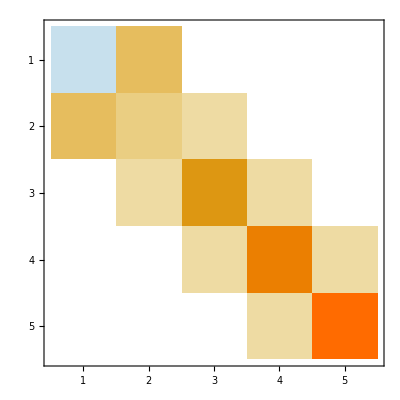

```mathematica
hEvenPMatrix//MatrixPlot
```

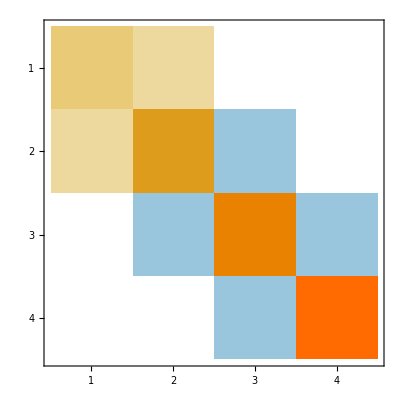

```mathematica
hOddPMatrix//MatrixPlot
```

```mathematica
hOddPMatrix//MatrixForm
```

(0.8335 | 0.707107 | 0. | 0.
0.707107 | 1.834 | -0.707107 | 0.
0. | -0.707107 | 2.5005 | -0.707107
0. | 0. | -0.707107 | 3.167)

```mathematica
hEvenPMatrix//MatrixForm
```

(-0.167 | 1. | 0. | 0. | 0.
1. | 0.8335 | 0.707107 | 0. | 0.
0. | 0.707107 | 1.834 | 0.707107 | 0.
0. | 0. | 0.707107 | 2.5005 | 0.707107
0. | 0. | 0. | 0.707107 | 3.167)

## Diagonalize the Hamiltonian

Get eigen energies in both parity sectors

```mathematica
Block[{esystemEvenP, esystemOddP},
esystemEvenP = Normal@hEvenPMatrix//Eigensystem ;
esystemOddP = Normal@hOddPMatrix//Eigensystem; 
evaluesEvenP=esystemEvenP⟦1⟧//Re;
evaluesOddP=esystemOddP⟦1⟧//Re;
(* For each eigenvector, stores coefficients of the expansion of the eigenvector in the basis specified above *)
evectorsEvenP= esystemEvenP⟦2⟧;
evectorsOddP= esystemOddP⟦2⟧;
];
```

```mathematica
evectorKetsEvenP = evenPSector.evectorsEvenP;
evectorKetsOddP = oddPSector.evectorsOddP;
```

```mathematica
E0EvenP = evaluesEvenP// Sort //First;
E0OddP = evaluesOddP // Sort // First;
E0=Min[E0EvenP, E0OddP]
```

-0.843328

```mathematica
-2.5250054124450987/J0
```

-3.0294

Prepare lists of (1) sorted and (2) sorted and shifted eigenenergies

```mathematica
evaluesEvenPSorted = evaluesEvenP// Sort;
evaluesOddPSorted =evaluesOddP // Sort;
evaluesEvenPShifted = (evaluesEvenP - E0) // Sort ;
evaluesOddPShifted = (evaluesOddP - E0) // Sort ;
```

```mathematica
evaluesEvenPShifted
```

{0.,1.74231,2.60361,3.4826,4.55612}

```mathematica
evaluesOddPShifted
```

{1.24858,2.45054,3.4541,4.55509}

```mathematica
conventionFileName["evaluesEvenPShifted", L, Λ1,Λ2, "txt"]
```

data_L2/evaluesEvenPShifted_L2_lmd1_1_lmd2_4.txt

```mathematica
Export[conventionFileName["evaluesEvenPShifted", L, Λ1,Λ2, "txt"], evaluesEvenPShifted,"Table"];
Export[conventionFileName["evaluesOddPShifted", L, Λ1,Λ2, "txt"], evaluesOddPShifted,"Table"];
```

Get the rotation matrices that diagonalize the Hamiltonian

## Get the eigenvectors in each parity sector, ordered by the corresponding eigenvalues

```mathematica
eValVecPairEvenP= SortBy[Partition[Riffle[evaluesEvenP,evectorsEvenP],2],First[#]&];
eValVecPairOddP = SortBy[Partition[Riffle[evaluesOddP,evectorsOddP],2],First[#]&];
```

```mathematica
If[verbose,eValVecPairEvenP//TableForm]
```

-0.843328 | 0.817815
-0.553111
0.155078
-0.034064
0.00600621
0.898978 | -0.47866
-0.510241
0.629679
-0.322396
0.100514
1.76028 | -0.299074
-0.576401
-0.332517
0.611066
-0.307161
2.63927 | 0.111001
0.3115
0.638512
0.415655
-0.556938
3.71279 | 0.0171972
0.0667217
0.247366
0.590534
0.76507

```mathematica
If[verbose,eValVecPairOddP//TableForm]
```

0.405251 | 0.839144
-0.508216
-0.187735
-0.0480668
1.60722 | 0.476874
0.521796
0.644225
0.292051
2.61078 | 0.254567
0.63984
-0.448314
-0.569925
3.71176 | 0.0602023
0.245052
-0.590545
0.766539

## Get the change-of-basis matrix that diagonalizes the Hamiltonian

```mathematica
{pEven, hEvenPMatrixDiag}=SchurDecomposition[hEvenPMatrix];
 {pOdd, hOddPMatrixDiag}=SchurDecomposition[hOddPMatrix];
```

```mathematica
(* shows the diagonalized Hamiltonians *)
If[verbose, Transpose[pEven].hEvenPMatrix.pEven //Chop//MatrixForm]
If[verbose, Transpose[pOdd].hOddPMatrix.pOdd//Chop//MatrixForm]
```

(-0.843328 | 0 | 0 | 0 | 0
0 | 0.898978 | 0 | 0 | 0
0 | 0 | 1.76028 | 0 | 0
0 | 0 | 0 | 2.63927 | 0
0 | 0 | 0 | 0 | 3.71279)

(0.405251 | 0 | 0 | 0
0 | 1.60722 | 0 | 0
0 | 0 | 2.61078 | 0
0 | 0 | 0 | 3.71176)

```mathematica
(* These columns correspond to the even-parity eigenvectors found above, up to an overall sign *)
If[verbose, pEven//MatrixForm]
```

(-0.817815 | -0.47866 | -0.299074 | -0.111001 | 0.0171972
0.553111 | -0.510241 | -0.576401 | -0.3115 | 0.0667217
-0.155078 | 0.629679 | -0.332517 | -0.638512 | 0.247366
0.034064 | -0.322396 | 0.611066 | -0.415655 | 0.590534
-0.00600621 | 0.100514 | -0.307161 | 0.556938 | 0.76507)

```mathematica
(* These columns correspond to the odd-parity eigenvectors found above, up to an overall sign *)
If[verbose, pOdd//MatrixForm]
```

(0.839144 | 0.476874 | 0.254567 | 0.0602023
-0.508216 | 0.521796 | 0.63984 | 0.245052
-0.187735 | 0.644225 | -0.448314 | -0.590545
-0.0480668 | 0.292051 | -0.569925 | 0.766539)

## Solve for the angles that approximate the ground state

```mathematica
R[θ1]={{Cos[θ1], -Sin[θ1], 0, 0}, {Sin[θ1], Cos[θ1], 0, 0}, {0, 0, 1, 0}, {0, 0,0, 1}}; 
R[θ2]={{1, 0, 0, 0}, {0, Cos[θ2], -Sin[θ2], 0}, {0, Sin[θ2], Cos[θ2], 0}, {0, 0,0, 1}}; 
R[θ3]={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[θ3], -Sin[θ3]}, {0, 0, Sin[θ3], Cos[θ3]}}; 
GSrot = R[θ3].R[θ2].R[θ1];
```

```mathematica
GSrot//MatrixForm
```

(Cos[θ1] | -Sin[θ1] | 0 | 0
Cos[θ2] Sin[θ1] | Cos[θ1] Cos[θ2] | -Sin[θ2] | 0
Cos[θ3] Sin[θ1] Sin[θ2] | Cos[θ1] Cos[θ3] Sin[θ2] | Cos[θ2] Cos[θ3] | -Sin[θ3]
Sin[θ1] Sin[θ2] Sin[θ3] | Cos[θ1] Sin[θ2] Sin[θ3] | Cos[θ2] Sin[θ3] | Cos[θ3])

## Make a plot for the Low-Lying Energy Spectrum

```mathematica
savagePlot=Module[{
(* map energies below max value *)
emax, 
(* spacing of ticks between zero and eMax *)
eTickStep,
(* min allowed spacing between ticks *)
eTickMinSpacing,
 (* padding between emin and lower plot range for the y-axis *)
eLowerPadding,
(* the plot of the energy spectrum will be like a stacked bar chart *)
(* the width of bars for either parity value *)
barWidth ,
(* spacing between the two bar stacks *)
barPadding, 
(* leftmost and rightmost point on the x-axis for the two bar stacks  *)
evenBoundL ,evenBoundR,
oddBoundL,oddBoundR, 
evenTick,oddTick ,
(* define y-axis ticks for the eigenenergies *)
energyTicks,
(* padding to determine the x-range of the plot *)
paddingL,paddingR,
plotRangeL ,plotRangeR,
energies,
plot1, plot1Noisy, plot2, plot2Noisy},
emax = 3.5;
eTickStep = 0.5;
eTickMinSpacing = 0.3;
eLowerPadding = 0.1; 
barWidth = 1.0;
barPadding = 0.3; 
evenBoundL = 0.7;
evenBoundR = evenBoundL + barWidth;
oddBoundL = evenBoundR + barPadding;
oddBoundR = oddBoundL + barWidth;
evenTick = 0.5(evenBoundL + evenBoundR);
oddTick = 0.5(oddBoundL + oddBoundR);
paddingL = 0.7;
paddingR = 2.0;
plotRangeL = evenBoundL - paddingL;
plotRangeR = oddBoundR + paddingR;
energies = Table[Select[list, #-E0 < emax &], 
{list,{evaluesEvenPSorted, evaluesOddPSorted}}];
energyTicks =SetAccuracy[SetPrecision[
DeleteDuplicates[Sort[Flatten[energies]], Abs[#1-#2] < eTickMinSpacing &],
3],3];(*Table[en, {en, E0, E0+emax, eTickStep}];*)
plot1 =ListLinePlot[Table[{{evenBoundL, en}, {evenBoundR, en}}, {en, energies[[1]]}], PlotStyle->Red];
plot2=ListLinePlot[Table[{{oddBoundL, en}, {oddBoundR, en}}, {en, energies[[2]]}], PlotStyle->Blue];
Clear[PlotLegends];
Needs["PlotLegends`"];
Show[
plot1, (* stacked bars for π=+1 parity eigenenergies *)
plot2, (* stacked bars for π=-1 parity eigenenergies *) 
Axes->False,(* remove horizontal line at the origin *)
PlotRange -> {{plotRangeL, plotRangeR},{E0 - eLowerPadding, E0+emax}},
AxesOrigin-> {plotRangeL, 0},
PlotLabel->Style["Low-Lying Energy Spectrum of\n1+1 discretized Schwinger Model", Black, FontSize->15],
Epilog->{Style[Text[StringForm["`1` spatial sites\nk = 0", L],{oddBoundR + 0.55(plotRangeR - oddBoundR),E0+emax / 1.50}],16],
(*Style[Text[StringForm["MC ΔE_1= `1`", 
NumberForm[evaluesOddPShifted⟦1⟧, {4,3}]],
{oddBoundR + 0.40(plotRangeR - oddBoundR),E0+emax / 4.0}],Directive[Black,16]],*)
{Black,Arrow[{{evenTick, evaluesEvenPSorted⟦1⟧},{oddTick, evaluesOddPSorted⟦1⟧}}]},
Style[Text[StringForm["ΔE_1= `1`", NumberForm[evaluesOddPShifted⟦1⟧, {4,3}]],
{1.00*evenTick, 0.90*1/2(evaluesOddPSorted⟦1⟧+evaluesEvenPSorted⟦1⟧)}],14],
Style[Text["E_0, E_0",{.60(evenTick+oddTick),.95*evaluesEvenPSorted⟦1⟧}],12],
Style[Text["E_1, E_1",{.95(evenTick+oddTick),.95*evaluesOddPSorted⟦1⟧}],12]
},
Frame->True,
FrameLabel->{None,Style["E",Black, FontSize-> 20],None,None},
FrameTicks->{{energyTicks,None}, {{{evenTick, Style["P=+1",16]}, {oddTick,Style["P=-1", 16]}}, {None, None}}},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 20]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]];
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

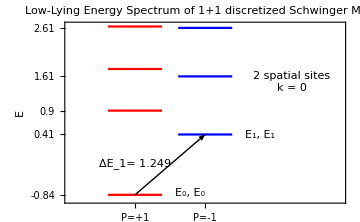

```mathematica
savagePlot
```

```mathematica
Block[{savagePlotFname},
savagePlotFname= conventionFileName["spectrumPlot", L, Λ1, Λ2, "png"];
If[!FileExistsQ[savagePlotFname], Export[savagePlotFname, savagePlot, ImageResolution-> imageRes]];
];
```

## Get the eigenstate ket expansion

Coefficients of the VQS expansion for the eigenstates

```mathematica
gsCoeffs = evectorsEvenP[[ Position[evaluesEvenP, E0][[1, 1]] ]] //Chop//Rationalize;
eEvenPCoeffs=Table[
(* find the index of the ith even-parity excited state in the array of the corresponding eigenvectors; each array element is a list of coefficients for the expansion of that eigenvector in terms of the original basis *)
evectorsEvenP⟦Position[evaluesEvenP, evaluesEvenPSorted⟦i⟧]⟦1, 1⟧ ⟧ //Chop//Rationalize,
(* note that the first element is the ground state *)
{i, 2, Length[evaluesEvenPSorted]}];
eOddPCoeffs=Table[
(* find the index of the ith even-parity excited state in the array of the corresponding eigenvectors; each array element is a list of coefficients for the expansion of that eigenvector in terms of the original basis *)
evectorsOddP⟦Position[evaluesOddP, evaluesOddPSorted⟦i⟧]⟦1, 1⟧ ⟧ //Chop//Rationalize,
{i, Length[evaluesOddPSorted]}];
e1Coeffs = eOddPCoeffs⟦1⟧;
```

```mathematica
GSapprox = GSrot.{1, 0, 0, 0};
```

```mathematica
(* changed sign here from pEven to -pEven to get Martin's results *)
thetaSol =Quiet[NSolve[Drop[Thread[GSapprox==-pEven⟦All, 1⟧], -1], {θ1, θ2, θ3}]];
NumberForm[First[thetaSol], 4]
(* compare with Martin's reported results of {θ1->-0.6130, θ2-> -0.2785, θ3-> -0.20844} *)
```

First::nofirst: {} has zero length and no first element.

First[{}]

```mathematica
NumberForm[thetaSol,4]
```

{}

```mathematica
evaluesEvenP
```

{3.71279,2.63927,1.76028,0.898978,-0.843328}

```mathematica
pEven⟦All, 1⟧
(GSrot /.{θ1->-0.6130, θ2-> -0.2785, θ3-> -0.20844})⟦All,1⟧
(GSrot /.{θ1->0.6130, θ2->0.2785, θ3->0.20844})⟦All,1⟧
```

{-0.817815,0.553111,-0.155078,0.034064,-0.00600621}

{0.817926,-0.553156,0.154741,-0.0327296}

{0.817926,0.553156,0.154741,0.0327296}

```mathematica
pEven⟦All, 1⟧
```

{-0.817815,0.553111,-0.155078,0.034064,-0.00600621}

Tables for expansions as visual guide

## Ground state

```mathematica
gsTable =ParallelTable[
{NumberForm[gsCoeffs⟦i⟧,{4,5}],
(* print the result of Hfield acting on the ket *)
Round[N[(1/J) * Hfield/.Ket[Ψ]->varBasis1⟦i⟧/.params//.rules].varBasis1⟦i⟧//.rules],
(* print the actual ket expansion converted to fermionic sites *)
varBasis1⟦i⟧}, {i, Length[varBasis1]}];
```

```mathematica
Block[{sortedTable},
sortedTable=Select[Simplify[gsTable],#⟦2⟧ ≤ Λ3+1 &];
gsTableForm = Grid[sortedTable,
 ItemSize->{{ 6.0, 1.5, 60},ConstantArray[3, Length[sortedTable]]}, Frame-> All]];
```

```mathematica
Block[{gsExpansionFname},
gsExpansionFname=  conventionFileName[ToString[StringForm["gsExpansion_lmd3_`1`", Λ3]], L, Λ1, Λ2, "png"];
If[!FileExistsQ[gsExpansionFname] ∧ verbose, Export[gsExpansionFname, gsTableForm, ImageResolution-> imageRes/3]];
];
```

```mathematica
If[verbose,gsTableForm]
```

0.81780 | 0 | 0,1,0,1,0,0,0,0
-0.55310 | 1 | 1/2 (0,0,1,1,0,-1,0,0+0,1,1,0,0,0,1,0+1,0,0,1,1,0,0,0+1,1,0,0,0,0,0,-1)
0.15510 | 2 | (1,0,1,0,0,-1,0,-1+1,0,1,0,1,0,1,0)/(√2)
-0.03406 | 3 | 1/2 (0,0,1,1,1,0,1,1+0,1,1,0,-1,-1,0,-1+1,0,0,1,0,-1,-1,-1+1,1,0,0,1,1,1,0)
0.00601 | 4 | (0,1,0,1,-1,-1,-1,-1+0,1,0,1,1,1,1,1)/(√2)

Probabilities of measuring the ground state in the calculational basis of VQS are the squares of the coefficients; they of course are normalized to 1.

```mathematica
gsCoeffs^2
gsCoeffs.gsCoeffs
```

{0.668822,0.305932,0.0240493,0.00116035,0.0000360745}

1.

## Lightest Vector Meson

```mathematica
e1OddTable =ParallelTable[
{NumberForm[eOddPCoeffs⟦1⟧⟦i⟧,{4, 5}],
(* print the result of Hfield acting on the ket *)
Round[N[(1/J) * Hfield/.Ket[Ψ]->varBasis2⟦i⟧/.params//.rules].varBasis2⟦i⟧//.rules],
(* print the actual ket expansion converted to fermionic sites *)
varBasis2⟦i⟧}, {i, Length[varBasis2]}];
```

```mathematica
Block[{sortedTable},
sortedTable=Select[Simplify[e1OddTable],#⟦2⟧ ≤ Λ3 +1&];
e1OddTableForm = Grid[sortedTable,
 ItemSize->{{ 6.0, 1.5, 60},ConstantArray[3, Length[sortedTable]]}, Frame-> All]];
```

```mathematica
Block[{e1ExpansionFname},
e1ExpansionFname=  conventionFileName[ToString[StringForm["e1Expansion_lmd3_`1`", Λ3]], L, Λ1, Λ2, "png"];
If[!FileExistsQ[e1ExpansionFname], Export[e1ExpansionFname, e1OddTableForm, ImageResolution-> imageRes/3]];
];
```

```mathematica
If[verbose,e1OddTableForm]
```

0.83910 | 1 | 1/2 (0,0,1,1,0,-1,0,0-0,1,1,0,0,0,1,0-1,0,0,1,1,0,0,0+1,1,0,0,0,0,0,-1)
-0.50820 | 2 | (1,0,1,0,0,-1,0,-1-1,0,1,0,1,0,1,0)/(√2)
-0.18770 | 3 | 1/2 (0,0,1,1,1,0,1,1-0,1,1,0,-1,-1,0,-1-1,0,0,1,0,-1,-1,-1+1,1,0,0,1,1,1,0)
-0.04807 | 4 | (0,1,0,1,-1,-1,-1,-1-0,1,0,1,1,1,1,1)/(√2)

```mathematica
e1Coeffs
```

{0.839144,-0.508216,-0.187735,-0.0480668}

```mathematica
e1Coeffs^2
e1Coeffs.e1Coeffs
```

{0.704162,0.258283,0.0352443,0.00231042}

1.

Define functions to extract coefficients of the expansions in the VQS basis

```mathematica
Block[{basisGaussSorted},
basisGaussSorted=SortBy[basisGauss, ((1/J) * Hfield/.Ket[Ψ]->#/.params//.rules).# //.rules&];
computBasis = S.# //.rules &/@ basisGaussSorted;
];
```

```mathematica
fluxesComputBasisSorted = ParallelTable[((1/J) * Hfield/.Ket[Ψ]-> basisKet/.params//.rules).basisKet //.rules,{basisKet, computBasis}];
```

```mathematica
computeOpOnState[op_, onState_]:=Expand[op/.state-> onState //.rules];
```

```mathematica
(* 
Given an eigenstate expansion (with kets), produces a list of (non-normalized) coefficients, without kets, in the computational basis; 
the list is loaded if file already exists, or computed and saved in a file otherwise.
 *)
extractCoeffs[estate_, fname_String]:=
Block[{coeffsFname,coeffs, ctr, len, indicator},
coeffsFname=conventionFileName[fname, L, Λ1, Λ2, "txt"];
If[!FileExistsQ[coeffsFname],
(* if the file with coefficients does not yet exist, compute it... *)
ctr=0;
len = Length[computBasis];
indicator = ToString[StringForm["Extracting coeffs for `1`:", fname]];
SetSharedVariable[ctr];
coeffs = Monitor[
ParallelTable[N[Coefficient[estate,computBasis⟦i⟧]],{i, len}],
Row[{indicator, ProgressIndicator[ctr, {1, len}], ctr, "/", len}," "]];
(* ... and save it. *)
Export[coeffsFname, coeffs,"List"],
(* else, load it *)
coeffs = Import[coeffsFname, "List"]];
Return[coeffs];
];
```

Get the coefficient arrays for the eigenstates

```mathematica
gs = Table[gsCoeffs⟦i⟧ * varBasis1⟦i⟧, {i, Length[varBasis1]}];
eOddP = Table[
Table[eOddPCoeffs⟦j⟧⟦i⟧ * varBasis2⟦i⟧//. rules, {i, Length[varBasis2]}],
{j, 1, Length[varBasis2]}];
eEvenP = Table[
Table[eEvenPCoeffs⟦j⟧⟦i⟧ * varBasis1⟦i⟧//. rules, {i, Length[varBasis1]}],
{j, 1, Length[varBasis1]-1}];
```

### Ground state

```mathematica
ClearAll[gsCoeffsCompBasis];
Block[{expandedState, fname, norm},
expandedState = Expand[Total[gs]];
fname = "gsCoeffsCompBasis";
gsCoeffsCompBasis=Normalize[extractCoeffs[expandedState,fname]];
];
```

### All excited even parity states

```mathematica
ClearAll[eEvenPCoeffsCompBasis];
Monitor[For[istate = 1,istate ≤ Length[eEvenP],istate++,
Block[{expandedState, fname},
expandedState = Expand[Total[eEvenP⟦istate⟧]]; (* !!! IMPORTANT TO EXPAND !!! *)
fname = ToString[StringForm["eEvenPCoeffsCompBasis_`1`", istate]];
eEvenPCoeffsCompBasis[istate]=Normalize[extractCoeffs[expandedState,fname]];
];],
Row[{ProgressIndicator[istate, {1, Length[eEvenP]}], istate, "/", Length[eEvenP]}," "]];
```

### All excited odd parity states

```mathematica
ClearAll[eOddPCoeffsCompBasis];
Monitor[For[istate = 1,istate ≤ Length[eOddP],istate++,
Block[{expandedState, fname},
expandedState = Expand[Total[eOddP⟦istate⟧]]; (* !!! IMPORTANT TO EXPAND !!! *)
fname = ToString[StringForm["eOddPCoeffsCompBasis_`1`", istate]];
eOddPCoeffsCompBasis[istate]=Normalize[extractCoeffs[expandedState,fname]];
];],
Row[{ProgressIndicator[istate, {1, Length[eOddP]}], istate, "/", Length[eOddP]}," "]];
```

## Define interpolating operators

Preliminaries

## Expansions of low-lying eigenstates in the computations basis (with kets, not just coefficients)

```mathematica
gsExpanded=Expand[Total[gs]];
e1Expanded = Expand[Total[eOddP⟦1⟧]];
e2Expanded = Expand[Total[eEvenP⟦1⟧]];
```

## Finding the action of the operator on a state expansion

```mathematica
(* NB: this does not normalize the resulting state (performance reasons, don't want to normalize at intermediate steps) *)
findAction[op_,onState_]:= Expand[(* This expand is slow but important: need to group kets to read off their coefficients *)
op/.state-> onState//.rules]//.rules;
```

## SLOW: Finding the overlap onto a target state

```mathematica
findOvlap[fromState_, opSrc_, opSnk_, toState_]:=
If[!excludeSlow,
Block[{srcOvlap, snkOvlap, srcTerm,snkNorm, srcNorm, snkTerm},
Print["Computing the source term..."];
srcTerm = findAction[opSrc, fromState];
Print["Normalizing the the source term..."];
srcNorm=Sqrt[srcTerm.srcTerm//.rules]//.rules;
srcTerm = srcTerm /srcNorm;
Print["Calculating the source overlap..."];
srcOvlap = srcTerm.toState//.rules;
Print["Computing the sink term..."];
snkTerm = findAction[opSnk, fromState];
Print["Normalizing the the sink term..."];
snkNorm=Sqrt[snkTerm.snkTerm//.rules]//.rules;
snkTerm = snkTerm /snkNorm;
Print["Calculating the sink overlap..."];
snkOvlap= snkTerm.toState//.rules;
Print["Overlap for {source, sink} is"];
Print[{srcOvlap, snkOvlap}];],
Print["This function won't run for too large a chain..."]];
```

“Naive” interpolating operators

## Chiral density

```mathematica
ClearAll[χ0Src,χ0Snk];
χ0Src[i_]:= 1/L(-1)^(i+1)SubPlus[χ][i].SubMinus[χ][i].state ;
χ0Snk= Sum[χ0Src[i] , {i, 1, nfs, 2}];
```

```mathematica
findOvlap[gsExpanded, 
χ0Src[srcInsertionSite],
χ0Snk,
e2Expanded
]
```

Computing the source term...

Normalizing the the source term...

Calculating the source overlap...

Computing the sink term...

Normalizing the the sink term...

Calculating the sink overlap...

Overlap for {source, sink} is

{-0.269335,-0.282862}

## “Hopping Density”

```mathematica
ClearAll[M01DagSrc,M01DagSnk];
M01Src[i_] :=(α[fs[i],fs[i-1]].state-α[fs[i], fs[i+1]].state);
M01Snk =Sum[M01Src[i], {i,1, nfs-1, 2}];
M01DagSrc[i_] :=(α[fs[i-1],fs[i]].state-α[fs[i+1], fs[i]].state);
M01DagSnk =Sum[M01DagSrc[i], {i,1, nfs-1, 2}];
```

```mathematica
findOvlap[gsExpanded, 
M01Src[srcInsertionSite],
M01Snk,
e1Expanded
]
```

Computing the source term...

Normalizing the the source term...

Calculating the source overlap...

Computing the sink term...

Normalizing the the sink term...

Calculating the sink overlap...

Overlap for {source, sink} is

{-0.718625,-0.972765}

```mathematica
findOvlap[gsExpanded, 
M01DagSrc[srcInsertionSite],
M01DagSnk,
e1Expanded
]
```

Computing the source term...

Normalizing the the source term...

Calculating the source overlap...

Computing the sink term...

Normalizing the the sink term...

Calculating the sink overlap...

Overlap for {source, sink} is

{-0.31851,-0.447781}

Quantum-Improved IOs

```mathematica
Length[varBasis1]
```

5

## Preliminaries --- UNUSED WITH LINK OPERATORS

### Get the operator indices

```mathematica
opCoeffIndices[flux_Integer, fluxSectorSorted_, opFluxIndices_]:=Block[{start, finish},
start = 1 + Sum[Length[fluxSectorSorted[f]], {f, 0, flux - 1}];
finish = start + Length[opFluxIndices[flux]] - 1;
Table[i, {i,start, finish}]
]
```

### Get the flux of the ket from the operator index

```mathematica
(* given an term index from an operator and the corresponding opFluxIndices: flux -> list of operator indices, returns the flux sector that contains the term corresponding to the given index; otherwise returns -1 *)
fluxSecFromOpIndex[index_, opFluxIndices_]:=For[flux = 0, flux ≤ Λ3,flux++,If[MemberQ[opFluxIndices[flux],index],Return[flux],Continue]; If[flux == Λ3,Return[-1]]];
```

## Flux-Link Operator: Ground State ⇒ First Excited State

### Optimize the variational basis of operators

#### Vector of kets in the MC basis

```mathematica
optTableUnpruned=Select[Table[{ 
eOddPCoeffsCompBasis[1]⟦i⟧/gsCoeffsCompBasis⟦i⟧,
eOddPCoeffsCompBasis[1]⟦i⟧,(* E1 weight, including normalization factor *)
gsCoeffsCompBasis⟦i⟧,              (* E0 weight, including normalization factor *)
Round[N[(1/J) * Hfield/.Ket[Ψ]->computBasis⟦i⟧/.params//.rules].computBasis⟦i⟧//.rules], (* flux sector *)
Total[computBasis⟦i⟧⟦nfs+1;;2nfs⟧], (* sum of all links *)
computBasis⟦i⟧},
{i, Length[computBasis]}],
Abs[#⟦4⟧]≤Λ2& (* consider less flux sectors (harsher truncation on the operator construction) *)
];
(* split into flux sectors, sort according to the weights inside each *)
optTableUnpruned=Split[optTableUnpruned,#1⟦4⟧==#2⟦4⟧&];
optTableUnpruned=Flatten[SortBy[-Abs[#⟦2⟧] &]/@optTableUnpruned, 1];
(* delete elements if weights in E0 and E1 and the flux sectors and the sum of all links all coincide *)
optTable =optTableUnpruned;(*DeleteDuplicates[optTableUnpruned, #1⟦2⟧==#2⟦2⟧ ∧ #1⟦3⟧==#2⟦3⟧ ∧Abs[#1⟦4⟧]==Abs[#2⟦4⟧]∧Abs[#1⟦5⟧]==Abs[#2⟦5⟧]&];*)
optVec = optTable⟦All, 6⟧;(* vector of kets *)
optFlux = optTable⟦All, 4⟧; (* vector of flux sectors *)
e1Coeff=optTable⟦All, 2⟧;(* target coeff   *)
e0Coeff=optTable⟦All, 3⟧; (* starting coeff *)
```

```mathematica
TableForm[optTable,TableHeadings->{Table[j, {j, 1, Length[optTable]}],
{"θ_(π = -1)/θ_(π = +1)", "θ_(π = -1)", "θ_(π = +1)", "∑(ℓ^2)_i", "∑ℓ_i", "ψ"}}];
```

```mathematica
fluxTruncLen=Length[Select[optFlux, #≤Λ2&]] (* number of kets in the harshly truncated space*)
```

13

#### Variational basis of operators

```mathematica
ClearAll[lnkOpSrc,lnkOpSnk,lnkOpVec,lnkOpVecSrc]
```

```mathematica
(* FLUX 1 *)
nlnkOpVecFlux[1]=1;
lnkOpSrc[1][1][i_]:=-l[fs[i]].state-l[fs[i-1]].state;
lnkOpSnk[1][1]=Sum[lnkOpSrc[1][1][i],{i,1,nfs-1,2}];
lnkOpVec[1][1]=Block[{opOnState},
opOnState=(Expand[lnkOpSnk[1][1]/.state-> #] //.rules) & /@ optVec;
MapThread[If[#1===0, 0, #1.#2 //.rules]&,{opOnState,optVec}]
];
lnkOpVecSrc[1][1]=Block[{opOnState},
opOnState=(Expand[lnkOpSrc[1][1][1]/.state-> #] //.rules) & /@ optVec;
MapThread[If[#1===0, 0, #1.#2 //.rules]&,{opOnState,optVec}]
];
```

```mathematica
(* FLUX 2 *)
nlnkOpVecFlux[2]=2;(*L/2;*)
lnkOpSrc[2][k_Integer][i_]/;1≤k≤nlnkOpVecFlux[2]:=
l[fs[i]].l[fs[i+2k]].state-l[fs[i-1]].l[fs[i-1-2k]].state;(*-norm[k]^2/2(l[fs[i]] + l[fs[i+2k]]).l[fs[i]].l[fs[i+2k]].state-norm[k]^2/2(l[fs[i-1]] + l[fs[i-1-2k]]).l[fs[i-1]].l[fs[i-1-2k]].state;*)
lnkOpSnk[2][k_Integer]/;1≤k≤nlnkOpVecFlux[2]:=Sum[lnkOpSrc[2][k][i],{i,1,nfs-1,2}];
For[k=1,k≤nlnkOpVecFlux[2],k++,
lnkOpVec[2][k]=Block[{opOnState},
opOnState=(Expand[lnkOpSnk[2][k]/.state-> #] //.rules) & /@ optVec;
MapThread[If[#1===0, 0, #1.#2 //.rules]&,{opOnState,optVec}]
];
lnkOpVecSrc[2][k]=Block[{opOnState},
opOnState=(Expand[lnkOpSrc[2][k][1]/.state-> #] //.rules) & /@ optVec;
MapThread[If[#1===0, 0, #1.#2 //.rules]&,{opOnState,optVec}]
]
];
```

```mathematica
(* FLUX 3 *)
nlnkOpVecFlux[3]=3;
(* 1 *)
lnkOpSrc[3][1][i_]:=-l[fs[i]].l[fs[i+1]].l[fs[i+2]].state-l[fs[i-1]].l[fs[i-2]].l[fs[i-3]].state;
lnkOpSnk[3][1]=Sum[lnkOpSrc[3][1][i],{i,1,nfs-1,2}];
(* 2 *)
lnkOpSrc[3][2][i_]:=-l[fs[i-2]].l[fs[i]].l[fs[i+2]].state-l[fs[i-1+2]].l[fs[i-1]].l[fs[i-1-2]].state;
lnkOpSnk[3][2]=Sum[lnkOpSrc[3][2][i],{i,1,nfs-1,2}];
(* 3 *)
lnkOpSrc[3][3][i_]:=-l[fs[i]].l[fs[i+2]].l[fs[i+2+3]].state-l[fs[i-1]].l[fs[i-1-2]].l[fs[i-1-2-3]].state;
lnkOpSnk[3][3]=Sum[lnkOpSrc[3][3][i],{i,1,nfs-1,2}];
(* vector *)
For[k=1,k≤nlnkOpVecFlux[3],k++,
lnkOpVec[3][k]=Block[{opOnState},
opOnState=(Expand[lnkOpSnk[3][k]/.state-> #] //.rules) & /@ optVec;
MapThread[If[#1===0, 0, #1.#2 //.rules]&,{opOnState,optVec}]
];
lnkOpVecSrc[3][k]=Block[{opOnState},
opOnState=(Expand[lnkOpSrc[3][k][1]/.state-> #] //.rules) & /@ optVec;
MapThread[If[#1===0, 0, #1.#2 //.rules]&,{opOnState,optVec}]
]
];
```

```mathematica
Clear[optOpList,optOpSrcList,lnkOpSrcList, lnkOpSnkList]
(* TRUNCATED VERSION *)
optOpList = Flatten[Table[lnkOpVec[flux][nop]⟦;;fluxTruncLen⟧,{flux, 3}, {nop, 1, nlnkOpVecFlux[flux]}], 1];
optOpSrcList=Flatten[Table[lnkOpVecSrc[flux][nop]⟦;;fluxTruncLen⟧,{flux, 3}, {nop, 1, nlnkOpVecFlux[flux]}], 1];
(* FULL VERSION FOR GEVP *)
optOpListFull = Flatten[Table[lnkOpVec[flux][nop],{flux, 3}, {nop, 1, nlnkOpVecFlux[flux]}], 1];
optOpSrcListFull=Flatten[Table[lnkOpVecSrc[flux][nop],{flux, 3}, {nop, 1, nlnkOpVecFlux[flux]}], 1];
(* OPERATOR LIST *)
lnkOpSrcList = Flatten[Flatten[Table[lnkOpSrc[flux][nop],{flux, 3}, {nop, 1, nlnkOpVecFlux[flux]}], 1]];
lnkOpSnkList= Flatten[Flatten[Table[lnkOpSnk[flux][nop],{flux, 3}, {nop, 1, nlnkOpVecFlux[flux]}], 1]];
```

#### Find optimal constructions

Optimizing in a harshly truncated space

```mathematica
(* NB: optimization is performed in a harshly truncated space *)
iniConfig = Flatten[{1, Table[0, Length[optOpList]-1]}];
optIniState= Normalize[Total[iniConfig *optOpList,1] *Normalize[e0Coeff⟦;;fluxTruncLen⟧]];
optIniSrcState= Normalize[Total[iniConfig *optOpSrcList,1] *Normalize[e0Coeff⟦;;fluxTruncLen⟧]];
optTargetState =Normalize[e1Coeff⟦;;fluxTruncLen⟧];
```

```mathematica
optFunc[α_]:=Abs[
(optTargetState.(Normalize[Total[α *optOpList,1] * Normalize[e0Coeff⟦;;fluxTruncLen⟧]]))
];
optArgs = Table[α[i], {i, 1, Length[iniConfig]}];
optIniPoint= Table[{α[i],iniConfig⟦i⟧},  {i, 1, Length[iniConfig]}];
optConfig =Normalize[FindArgMin[1-optFunc[optArgs], optIniPoint, Method-> "PrincipalAxis"]]
```

{0.977634,0.078556,-0.121639,0.151912,-0.0100354,0.00933091}

```mathematica
(*optConfig=Get[conventionFileName["optConfig", L, Λ1, Λ3Noise, "txt"]]*)
```

```mathematica
nNoisySamples=200;
```

```mathematica
If[!recomputeNoise, 
ClearAll[noisyConfig];
For[sample=1,sample ≤ nNoisySamples, ++sample,
noisyConfig[sample]=Import[conventionFileName[
ToString[StringForm["noisyConfig_`1`",sample]], 
L, Λ1, Λ3Noise, "txt"], "List"];
];
];
```

Estimate how good the constructions are based on the overlap onto the target state (in a harshly truncated s

```mathematica
SetPrecision[optFunc[iniConfig],9] (* initial guess --- effectively, a single-operator link field construction *)
```

0.998971492

```mathematica
SetPrecision[optFunc[optConfig],9] (* optimized construction *)
```

1.

```mathematica
(* optimized construction with NOISE *)
If[recomputeNoise, 
Mean[Table[optFunc[noisyConfig[sample]], {sample, 1, nNoisySamples}]]
StandardDeviation[Table[optFunc[noisyConfig[sample]], {sample, 1, nNoisySamples}]]
];
```

### Define the operators acting on states

```mathematica
Clear[lnkOpSimpleSrcSummed,lnkOpSimpleSnkSummed];
lnkOpSimpleSrcSummed[i_]:=Expand[lnkOpSrcList⟦1⟧[i]]
lnkOpSimpleSnkSummed=Expand[lnkOpSnkList⟦1⟧];
```

```mathematica
Clear[lnkOpSrcSummed,lnkOpSnkSummed];
lnkOpSrcSummed[i_]:=Expand[Total[Table[optConfig⟦nop⟧*lnkOpSrcList⟦nop⟧[i],{nop, 1, Length[optConfig]}]]]
lnkOpSnkSummed=Expand[Total[optConfig*lnkOpSnkList]];
```

```mathematica
If[recomputeNoise, 
Clear[lnkOpNoisySrcSummed,lnkOpNoisySnkSummed];
lnkOpNoisySrcSummed[sample_][i_]:=Expand[Total[Table[noisyConfig[sample]⟦nop⟧*lnkOpSrcList⟦nop⟧[i],{nop, 1, Length[optConfig]}]]];
lnkOpNoisySnkSummed[sample_]:=Expand[Total[noisyConfig[sample]*lnkOpSnkList]];
];
```

### Find all matrix terms for the GEVP

```mathematica
Clear[lnkOpSrcClas,lnkOpSnkClas];
lnkOpSrcClas[i_]:=Table[lnkOpSrcList⟦nop⟧[i],{nop, 1, Length[optConfig]}];
lnkOpSnkClas=Table[lnkOpSnkList⟦nop⟧,{nop, 1, Length[optConfig]}];
```

## Compute effective mass with interpolating operators

Preliminaries

## Action of operators on GS

### Naive

#### Chiral Condensate

```mathematica
If[!FileExistsQ[conventionFileName["chi0SrcOnGSCompBasis", L, Λ1, Λ2, "txt"]],
χ0SrcOnGS=findAction[χ0Src[srcInsertionSite],gsExpanded];
];
If[!FileExistsQ[conventionFileName["chi0SnkOnGSCompBasis", L, Λ1, Λ2, "txt"]],
χ0SnkOnGS =findAction[χ0Snk,gsExpanded];
];
```

#### Hopping Density

```mathematica
If[!FileExistsQ[conventionFileName["M01SrcOnGSCompBasis", L, Λ1, Λ2, "txt"]],
M01SrcOnGS=findAction[M01Src[srcInsertionSite],gsExpanded];
];
If[!FileExistsQ[conventionFileName["M01SnkOnGSCompBasis", L, Λ1, Λ2, "txt"]],
M01SnkOnGS=findAction[M01Snk,gsExpanded];
];
```

```mathematica
If[!FileExistsQ[conventionFileName["M01DagSrcOnGSCompBasis", L, Λ1, Λ2, "txt"]],
M01DagSrcOnGS=findAction[M01DagSrc[srcInsertionSite],gsExpanded];
];
If[!FileExistsQ[conventionFileName["M01DagSnkOnGSCompBasis", L, Λ1, Λ2, "txt"]],
M01DagSnkOnGS=findAction[M01DagSnk,gsExpanded];
];
```

### Link

#### Source and Sink terms

```mathematica
If[!FileExistsQ[conventionFileName["op3SimpleSrcOnGSCompBasis", L, Λ1, Λ2, "txt"]],
op3SimpleSrcOnGS=findAction[lnkOpSimpleSrcSummed[srcInsertionSite], gsExpanded];
];
```

```mathematica
If[!FileExistsQ[conventionFileName["op3SimpleSnkOnGSCompBasis", L, Λ1, Λ2, "txt"]],
op3SimpleSnkOnGS=findAction[lnkOpSimpleSnkSummed, gsExpanded];
];
```

```mathematica
If[!FileExistsQ[conventionFileName[
ToString[StringForm["op3SrcOnGSCompBasis_trunc_L`1`_lmd3_`2`", L,Λ3Noise]], 
L, Λ1, Λ2, "txt"]],
op3SrcOnGS=findAction[lnkOpSrcSummed[srcInsertionSite], gsExpanded];
];
```

```mathematica
If[!FileExistsQ[conventionFileName[
ToString[StringForm["op3SnkOnGSCompBasis_trunc_L`1`_lmd3_`2`", L,Λ3Noise]], 
L, Λ1, Λ2, "txt"]],
op3SnkOnGS=findAction[lnkOpSnkSummed, gsExpanded];
];
```

#### Matrix elements for the GEVP

```mathematica
op3SrcClasOnGS=Table[findAction[lnkOpSrcClas[srcInsertionSite]⟦nop⟧, gsExpanded],{nop, 1, Length[optConfig]}];
op3SnkClasOnGS=Table[findAction[lnkOpSnkClas⟦nop⟧, gsExpanded],{nop, 1, Length[optConfig]}];
```

#### Noisy operators

```mathematica
op3NoisySrcOnGS
```

```mathematica
If[recomputeNoise, 
ClearAll[op3NoisySrcOnGS,op3NoisySnkOnGS]
Monitor[For[sample = 1,sample ≤nNoisySamples,sample++,
(*Print[sample];*)
op3NoisySrcOnGS[sample]=findAction[lnkOpNoisySrcSummed[sample][srcInsertionSite], gsExpanded];
op3NoisySnkOnGS[sample]=findAction[lnkOpNoisySnkSummed[sample], gsExpanded]
],Row[{ProgressIndicator[sample, {1, nNoisySamples}], sample, "/", nNoisySamples}," "]]
];
```

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

## Calculate expansions of interpolating operators acting on | GS ⟩

### Naive

```mathematica
Block[{fname},
fname="chi0SrcOnGSCompBasis";
χ0SrcOnGSCompBasis=Normalize[extractCoeffs[χ0SrcOnGS,fname]];
];
```

```mathematica
Block[{fname},
fname="chi0SnkOnGSCompBasis";
χ0SnkOnGSCompBasis=Normalize[extractCoeffs[χ0SnkOnGS,fname]];
];
```

```mathematica
Block[{fname},
fname="M01SrcOnGSCompBasis";
M01SrcOnGSCompBasis=Normalize[extractCoeffs[M01SrcOnGS,fname]];
];
```

```mathematica
Block[{fname},
fname="M01SnkOnGSCompBasis";
M01SnkOnGSCompBasis=Normalize[extractCoeffs[M01SnkOnGS,fname]];
];
```

```mathematica
Block[{fname},
fname="M01DagSrcOnGSCompBasis";
M01DagSrcOnGSCompBasis=Normalize[extractCoeffs[M01DagSrcOnGS,fname]];
];
```

```mathematica
Block[{fname},
fname="M01DagSnkOnGSCompBasis";
M01DagSnkOnGSCompBasis=Normalize[extractCoeffs[M01DagSnkOnGS,fname]];
];
```

### Smart

```mathematica
Block[{fname},
fname="op3SimpleSrcOnGSCompBasis";
op3SimpleSrcOnGSCompBasis=Normalize[extractCoeffs[op3SimpleSrcOnGS,fname]];
];
```

```mathematica
Block[{fname},
fname="op3SimpleSnkOnGSCompBasis";
op3SimpleSnkOnGSCompBasis=Normalize[extractCoeffs[op3SimpleSnkOnGS,fname]];
];
```

```mathematica
Block[{fname},
fname=ToString[StringForm["op3SrcOnGSCompBasis_trunc_L`1`_lmd3_`2`", L,Λ3Noise]];
op3SrcOnGSCompBasis=Normalize[extractCoeffs[op3SrcOnGS,fname]];
];
```

```mathematica
Block[{fname},
fname=ToString[StringForm["op3SnkOnGSCompBasis_trunc_L`1`_lmd3_`2`", L,Λ3Noise]];
op3SnkOnGSCompBasis=Normalize[extractCoeffs[op3SnkOnGS,fname]];
];
```

```mathematica
Block[{fname},
For[sample = 1,sample ≤nNoisySamples,sample++,
fname=ToString[StringForm["op3NoisySrcOnGSCompBasis_`1`", sample]];
op3NoisySrcOnGSCompBasis[sample]=Normalize[extractCoeffs[op3NoisySrcOnGS[sample],fname]];
];
];
Block[{fname},
For[sample = 1,sample ≤nNoisySamples,sample++,
fname=ToString[StringForm["op3NoisySnkOnGSCompBasis_`1`", sample]];
op3NoisySnkOnGSCompBasis[sample]=Normalize[extractCoeffs[op3NoisySnkOnGS[sample],fname]];
];
];
```

```mathematica
ClearAll[op3SrcClasOnGSCompBasis,op3SrcClasOnGSNorm];
Block[{fname,unnormed},
For[nop = 1,nop ≤Length[optConfig],nop++,
fname=ToString[StringForm["op3SrcClasOnGSCompBasis_`1`", nop]];
unnormed=extractCoeffs[op3SrcClasOnGS⟦nop⟧,fname];
op3SrcClasOnGSNorm[nop]=Norm[unnormed];
op3SrcClasOnGSCompBasis[nop]=Normalize[unnormed];
];
];
```

```mathematica
ClearAll[op3SnkClasOnGSCompBasis, op3SnkClasOnGSNorm];
Block[{fname,unnormed},
For[nop = 1,nop ≤Length[optConfig],nop++,
fname=ToString[StringForm["op3SnkClasOnGSCompBasis_`1`", nop]];
unnormed=extractCoeffs[op3SnkClasOnGS⟦nop⟧,fname];
op3SnkClasOnGSNorm[nop]=Norm[unnormed];
op3SnkClasOnGSCompBasis[nop]=Normalize[unnormed];
];
];
```

## Get the overlaps

```mathematica
getOvlaps[stateOnGSCompBasis_]:=
Block[{gsOvlaps, eEvenPOvlaps, eOddPOvlaps},
gsOvlaps=gsCoeffsCompBasis.stateOnGSCompBasis;
eEvenPOvlaps = Table[eEvenPCoeffsCompBasis[i].stateOnGSCompBasis,{i, 1,Length[eEvenP]}];
eOddPOvlaps = Table[eOddPCoeffsCompBasis[i].stateOnGSCompBasis,{i, 1,Length[eOddP]}];
Return[Join[{gsOvlaps}, eEvenPOvlaps, eOddPOvlaps]];
];
```

### Naive operators

```mathematica
χ0SrcOvlaps=getOvlaps[χ0SrcOnGSCompBasis];
χ0SnkOvlaps=getOvlaps[χ0SnkOnGSCompBasis];
```

```mathematica
M01SrcOvlaps=getOvlaps[M01SrcOnGSCompBasis];
M01SnkOvlaps=getOvlaps[M01SnkOnGSCompBasis];
```

```mathematica
M01DagSrcOvlaps=getOvlaps[M01DagSrcOnGSCompBasis];
M01DagSnkOvlaps=getOvlaps[M01DagSnkOnGSCompBasis];
```

### Link operators, source and sink

```mathematica
op3SimpleSrcOvlaps=getOvlaps[op3SimpleSrcOnGSCompBasis];
op3SimpleSnkOvlaps=getOvlaps[op3SimpleSnkOnGSCompBasis];
```

```mathematica
op3SrcOvlaps=getOvlaps[op3SrcOnGSCompBasis];
op3SnkOvlaps=getOvlaps[op3SnkOnGSCompBasis];
```

### Noisy link operators

```mathematica
For[sample = 1,sample ≤nNoisySamples,sample++,
op3NoisySrcOvlaps[sample]=getOvlaps[op3NoisySrcOnGSCompBasis[sample]];
op3NoisySnkOvlaps[sample]=getOvlaps[op3NoisySnkOnGSCompBasis[sample]];
];
```

### Matrix elements for the GEVP

```mathematica
For[nop = 1,nop ≤Length[optConfig],nop++,
op3SrcClasOvlaps[nop]=getOvlaps[op3SrcClasOnGSCompBasis[nop]];
op3SnkClasOvlaps[nop]=getOvlaps[op3SnkClasOnGSCompBasis[nop]];
];
```

## Generalized Eigenvalue Problem for Classical Variational Approach

### Get the energy estimate and the combination of operators to be used --- [0902.1265v2]

```mathematica
cMat[tau_]:=Block[{energies, cmat},
energies=Join[evaluesEvenPShifted, evaluesOddPShifted];
cmat = Table[Sum[op3SnkClasOvlaps[i]⟦n⟧*op3SnkClasOvlaps[j]⟦n⟧ *
Exp[-(energies⟦n⟧ - energies⟦1⟧) * t0 * tau],
{n, 2, Length[energies]}],{i, 1, Length[optConfig]},{j, 1, Length[optConfig]}];
Return[cmat];
];
```

```mathematica
tau0 = 5;  (* some initial time Subscript[τ, 0] at which excited state contributions are suppressed *)
cMat[tau0]//MatrixForm
```

(0.286499 | 0.151241 | 0.283993 | 0.0492646 | 0.151768 | 0.0492646
0.151241 | 0.127804 | 0.146424 | 0.0550453 | 0.128579 | 0.0550453
0.283993 | 0.146424 | 0.282243 | 0.0423737 | 0.146727 | 0.0423737
0.0492646 | 0.0550453 | 0.0423737 | 0.0663273 | 0.0573169 | 0.0663273
0.151768 | 0.128579 | 0.146727 | 0.0573169 | 0.129487 | 0.0573169
0.0492646 | 0.0550453 | 0.0423737 | 0.0663273 | 0.0573169 | 0.0663273)

```mathematica
(* "effective mass" *)
ClearAll[eEff]
npvalues= 3; (* number of principal values to compute *)
eEff[τ_, τ0_]:=Block[{e1, e2, λ1,λ2,α1, α2,eEff},
e1=Eigensystem[{cMat[τ],cMat[τ0]}, npvalues, 
Method-> {"Direct" }];
e2=Eigensystem[{cMat[τ+1],cMat[τ0]}, npvalues,
Method-> {"Direct"}];
λ1=Table[e1⟦1,i⟧, {i, 1, npvalues}];
λ2=Table[e2⟦1,i⟧, {i, 1, npvalues}];
α1=Table[e1⟦2,i⟧, {i, 1, npvalues}];
α2=Table[e2⟦2,i⟧, {i, 1, npvalues}];
eEff=Table[-1/t0(Log[λ2⟦i⟧]-Log[λ1⟦i⟧]), {i, 1,npvalues }];
Return[{eEff, α1}];
];
```

```mathematica
(* GEVP gets correct eigenenergies *)
```

```mathematica
{effGap, GEVPConfig}=eEff[2*tau0, tau0];
effGap
evaluesOddPShifted⟦;;npvalues⟧
```

{1.24858,2.45054,3.4541}

{1.24858,2.45054,3.4541}

```mathematica
(* eigenvector is NOT too different from Q-improved, once you take the normalization into account! *)
-GEVPConfig⟦1⟧
Normalize[Table[op3SrcClasOnGSNorm[i] * optConfig⟦i⟧, {i, 1, Length[optConfig]}]]
```

{0.994108,0.0664744,-0.0784253,0.0159353,-0.0303865,0.00180265}

{0.991956,0.0298242,-0.122573,0.00977707,-0.00382088,0.000600541}

```mathematica
(* the resulting vectors are cMat[tau0] - orthogonal: *)
GEVPConfig⟦1⟧.cMat[tau0].GEVPConfig⟦2⟧
GEVPConfig⟦1⟧.cMat[tau0].GEVPConfig⟦3⟧
GEVPConfig⟦2⟧.cMat[tau0].GEVPConfig⟦3⟧
```

3.59955×10^-17

2.97071×10^-17

-3.46945×10^-17

### Get the overlaps with GEVP-optimized combination

#### Define the operators

```mathematica
(*Clear[lnkOpSrcGEVPSummed,lnkOpSnkGEVPSummed];
For[evalue = 1, evalue ≤npvalues, ++evalue,
lnkOpSrcGEVPSummed[evalue, i_]:=Expand[Total[Table[GEVPConfig⟦evalue, nop⟧*lnkOpSrcList⟦nop⟧[i],{nop, 1, Length[optConfig]}]]];
lnkOpSnkGEVPSummed[evalue]=Expand[Total[GEVPConfig⟦evalue⟧*lnkOpSnkList]];
];*)
```

#### Compute their action on the ground state

```mathematica
(*ClearAll[op3SrcGEVPOnGS, op3SnkGEVPOnGS];
For[evalue = 1, evalue ≤npvalues, ++evalue,
(* src on GS *)
Block[{fname},
fname=ToString[StringForm["op3SrcGEVPOnGS_`1`", evalue]];
If[!FileExistsQ[conventionFileName[fname,  L, Λ1, Λ2, "txt"]],
op3SrcGEVPOnGS[evalue]=findAction[lnkOpSrcGEVPSummed[evalue,srcInsertionSite], gsExpanded];
];
];
(* snk on GS *)
Block[{fname},
fname=ToString[StringForm["op3SnkGEVPOnGS_`1`", evalue]];
If[!FileExistsQ[conventionFileName[fname, L, Λ1, Λ2, "txt" ]],
op3SnkGEVPOnGS[evalue]=findAction[lnkOpSnkGEVPSummed[evalue], gsExpanded];
];
];
];*)
```

#### Extract the coefficients in the computational basis

```mathematica
(*ClearAll[op3SrcGEVPOnGSCompBasis, op3SnkGEVPOnGSCompBasis];
For[evalue = 1, evalue ≤npvalues, ++evalue,
(* src on GS  *)
Block[{fname},
fname=ToString[StringForm["op3SrcGEVPOnGSCompBasis_`1`", evalue]];
op3SrcGEVPOnGSCompBasis[evalue]=Normalize[extractCoeffs[op3SrcGEVPOnGS[evalue],fname]]
];
(* snk on GS *)
Block[{fname},
fname=ToString[StringForm["op3SnkGEVPOnGSCompBasis_`1`", evalue]];
op3SnkGEVPOnGSCompBasis[evalue]=Normalize[extractCoeffs[op3SnkGEVPOnGS[evalue],fname]]
];
];*)
```

#### Finally get the overlaps

```mathematica
(*ClearAll[op3SrcGEVPOvlaps,op3SnkGEVPOvlaps]
For[evalue = 1, evalue ≤npvalues, ++evalue,
op3SrcGEVPOvlaps[evalue]=getOvlaps[op3SrcGEVPOnGSCompBasis[evalue]];
op3SnkGEVPOvlaps[evalue]=getOvlaps[op3SnkGEVPOnGSCompBasis[evalue]];
];*)
```

```mathematica
(* check the overlaps onto the odd-parity eigenstates *)
(*op3SnkGEVPOvlaps[1]⟦20;;⟧
op3SnkGEVPOvlaps[2]⟦20;;⟧
op3SnkGEVPOvlaps[3]⟦20;;⟧*)
```

#### Overlaps 2 (Phiala’s 07/02)

```mathematica
ClearAll[op3SrcGEVPOvlaps2,op3SnkGEVPOvlaps2]
Block[{srcOvlaps,snkOvlaps},
srcOvlaps=Table[op3SrcClasOvlaps[nop], {nop, Length[optConfig]}];
snkOvlaps=Table[op3SnkClasOvlaps[nop], {nop, Length[optConfig]}];
For[evalue = 1, evalue ≤npvalues, ++evalue,
op3SrcGEVPOvlaps2[evalue]=Total[GEVPConfig⟦evalue⟧ * srcOvlaps ,1];
op3SnkGEVPOvlaps2[evalue]=Total[GEVPConfig⟦evalue⟧ * snkOvlaps, 1];
];
];
```

```mathematica
Block[{fname},
fname=conventionFileName["GEVPSrc_ovlap", L, Λ1, Λ2, "txt"];
Export[fname, op3SrcGEVPOvlaps2[1],"Table"]
];
```

```mathematica
Block[{fname},
fname=conventionFileName["GEVPSnk_ovlap", L, Λ1, Λ2, "txt"];
Export[fname, op3SnkGEVPOvlaps2[1],"Table"]
];
```

```mathematica
(*test1= Normalize[op3SnkOvlaps]⟦20;;⟧;
test2 = Normalize[op3SnkGEVPOvlaps2[1]]⟦20;;⟧;
TableForm[Table[{test1⟦i⟧, -test2⟦i⟧}, {i, 1, Length[test1]}]]*)
```

## Define function to compute effective mass

```mathematica
ClearAll[g,gAsymm];
g[ovrlapSrc_,ovrlapSnk_, energies_,t_, T_]:=
Total[Table[ovrlapSrc⟦i⟧ *ovrlapSnk⟦i⟧ * 
( Exp[-(energies⟦i⟧ -energies⟦1⟧)*t]
+ Exp[-(energies⟦i⟧ -energies⟦1⟧)*(T - t)]), 
{i, 2, Length[energies]}]];
gAsymm[ovrlapSrc_,ovrlapSnk_,ovrlapDagSrc_,ovrlapDagSnk_, energies_,t_, T_]:=
Total[Table[
ovrlapSrc⟦i⟧ *ovrlapSnk⟦i⟧ * 
( Exp[-(energies⟦i⟧ -energies⟦1⟧)*t])
+ ovrlapDagSrc⟦i⟧ *ovrlapDagSnk⟦i⟧ *
(Exp[-(energies⟦i⟧ -energies⟦1⟧)*(T - t)]), 
{i, 2, Length[energies]}]];
```

```mathematica
ClearAll[computeEffMassNoCosh,computeEffMassAsymmNoCosh,computeEffMass,computeEffMassAsymm];
computeEffMassNoCosh[ovrlapSrc_,ovrlapSnk_,step_]:=
Block[{tList, energies,data,effMass},
tList = Table[t0 i, {i, 0, T/t0 -1}];
energies=Join[evaluesEvenPShifted, evaluesOddPShifted];
data = Table[g[ovrlapSrc,ovrlapSnk, energies, t, T], {t, tList}];
effMass= Table[1/(step t0)Log[data⟦i⟧/data⟦i+step⟧], {i, 1, Length[data]-step}];
Return[effMass]
];
computeEffMassAsymmNoCosh[ovrlapSrc_,ovrlapSnk_,ovrlapDagSrc_,ovrlapDagSnk_,step_]:=
Block[{tList, energies,data,effMass},
tList = Table[t0 i, {i, 0, T/t0 -1}];
energies=Join[evaluesEvenPShifted, evaluesOddPShifted];
data = Table[gAsymm[ovrlapSrc,ovrlapSnk,ovrlapDagSrc,ovrlapDagSnk, energies, t, T], {t, tList}];
effMass= Table[1/(step t0)Log[data⟦i⟧/data⟦i+step⟧], {i, 1, Length[data]-step}];
Return[effMass]
];
(* NO COSH CORRECTION AFTER ALL *)
computeEffMass[ovrlapSrc_,ovrlapSnk_,step_]:=
Block[{tList, energies,data,ilast, inext, effMass},
tList = Table[t0 i, {i, 0, T/t0-1}];
energies=Join[evaluesEvenPShifted, evaluesOddPShifted];
data = Table[g[ovrlapSrc,ovrlapSnk, energies, t, T], {t, tList}];
ilast[j_]:=If[j-step < 1, j-step +(Round[T/t0]), j-step];
inext[j_]:=If[j+step >Round[T/t0], j+step - (Round[T/t0]), j+step];
effMass= Table[
1/(step t0)Log[(data⟦i⟧)/(data⟦inext[i]⟧)], 
{i, 1, Length[data]-step}];
Return[Re[effMass]];
];
computeEffMassAsymm[ovrlapSrc_,ovrlapSnk_,ovrlapDagSrc_,ovrlapDagSnk_,step_]:=
Block[{tList, energies,data,ilast, inext, effMass},
tList = Table[t0 i, {i, 0, T/t0-1}];
energies=Join[evaluesEvenPShifted, evaluesOddPShifted];
data = Table[gAsymm[ovrlapSrc,ovrlapSnk,ovrlapDagSrc,ovrlapDagSnk, energies, t, T], {t, tList}];
ilast[j_]:=If[j-step < 1, j-step + (Round[T/t0]), j-step];
inext[j_]:=If[j+step >Round[T/t0], j+step - (Round[T/t0]), j+step];
effMass= Table[
1/(step t0)Log[(data⟦i⟧)/(data⟦inext[i]⟧)], 
{i, 1, Length[data]-step}];
Return[Re[effMass]];
];
```

Even Parity Gap

### Plot Settings

```mathematica
topPaddingE2 = 0.10;
botPaddingE2 = 0.10;
```

### Effective Mass and Exact Gap

```mathematica
gapE2=evaluesEvenPShifted⟦2⟧;
```

```mathematica
ClearAll[effMassE2Chi0]
effMassE2Chi0=computeEffMass[χ0SrcOvlaps, χ0SnkOvlaps, 1];
```

### Plots

```mathematica
ClearAll[gapE2Plot,effMassE2Chi0Data,effMassE2Chi0Plot];
gapE2Plot = Plot[gapE2, {x,0, T-1}, PlotStyle->Black,  PlotLegends->{"S^+ mass"},LabelStyle->{FontSize->  14}];
effMassE2Chi0Data = Table[{t0 * t, effMassE2Chi0⟦t+1⟧}, {t, 0, Floor[T/t0 -1]-1}];
effMassE2Chi0Plot= ListPlot[
effMassE2Chi0Data,
PlotLegends->{StringForm["naive Γ(τ)\n(Λ̃ = `1`)", Λ3]},
PlotStyle->Blue, LabelStyle->{FontSize->  14},
PlotMarkers-> {●}];
```

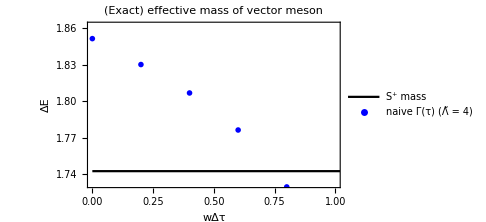

```mathematica
ClearAll[chi0Plot];
Block[{effMassE1Max, effMassE1Min, rangeE1, trange, irange},
trange = Floor[(T-1)/2];
irange=Floor[trange/t0];
effMassE1Max=Max[effMassE2Chi0⟦;;irange⟧];
effMassE1Min =gapE2;
rangeE1=effMassE1Max - effMassE1Min;
chi0Plot = Show[gapE2Plot,
effMassE2Chi0Plot,
 PlotRange -> {{0, trange}, {effMassE1Min-botPaddingE2 * rangeE1,effMassE1Max+topPaddingE2* rangeE1}},
PlotLabel->Style["(Exact) effective mass of vector meson", Black, FontSize->17],
Frame->True,
FrameTicks->Automatic,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]]
```

### Save data for combined plot

```mathematica
Block[{tab, fname},
tab=effMassE2Chi0Data;
fname=conventionFileName[ToString[StringForm["chi0_gap_T`1`",T]], L, Λ1, Λ2, "txt"];
Export[fname, tab,"Table"];
]
```

```mathematica
T/t0
```

20.

```mathematica
Table[effMassE2Chi0Data⟦2*i+1⟧, {i, 0, Floor[Length[effMassE2Chi0Data]/2]}]
```

{{0.,1.85143},{0.4,1.80669},{0.8,1.72933},{1.2,1.50566},{1.6,0.856862},{2.,-0.307695},{2.4,-1.256},{2.8,-1.64898},{3.2,-1.77619},{3.6,-1.8301}}

Odd Parity Gap

### Plot settings

```mathematica
topPaddingE1 = 0.10;
botPaddingE1 = 0.10;
```

### Effective mass and exact gap

#### Without Noise

```mathematica
ClearAll[gapE1,effMassE1M01,effMassE1Op3,effMassE1Op3Simple];
gapE1=evaluesOddPShifted⟦1⟧;
gapEOddP = Table[evaluesOddPShifted⟦evalue⟧,{evalue, 1, npvalues}];
effMassE1M01=computeEffMassAsymm[M01SrcOvlaps, M01SnkOvlaps,M01DagSrcOvlaps, M01DagSnkOvlaps,1];
effMassE1M01Symm=computeEffMass[M01SrcOvlaps, M01SnkOvlaps,1];
effMassE1Op3=computeEffMass[op3SrcOvlaps, op3SnkOvlaps,1];
effMassE1Op3Simple=computeEffMass[op3SimpleSrcOvlaps, op3SimpleSnkOvlaps,1];
```

```mathematica
ClearAll[effMassE10Op3GEVPPrincipal2];
For[evalue=1, evalue ≤npvalues, ++evalue,
effMassE10Op3GEVPPrincipal2[evalue]=computeEffMass[op3SrcGEVPOvlaps2[evalue],op3SnkGEVPOvlaps2[evalue],1];
]
```

#### Noisy mass

```mathematica
ClearAll[effMassE1Op3Noisy];
For[sample = 1,sample ≤nNoisySamples,sample++,
effMassE1Op3Noisy[sample]=computeEffMass[op3NoisySrcOvlaps[sample], op3NoisySnkOvlaps[sample],1];
];
ClearAll[effMassE1Op3NoisyAt];
For[time = 1,time ≤(T/t0)-1,time++,
effMassE1Op3NoisyAt[time]=Table[effMassE1Op3Noisy[sample]⟦time⟧,{sample, 1, nNoisySamples}];
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
If[recomputeNoise,
Manipulate[Block[{hist, smoothHist,
Q1,Q2,Q3,(* quartiles *)
rangeHistX, rangeHistY, rangeSmoothHistX, rangeSmoothHistY,
 minX, maxX, minY,maxY,
epsilon, rangeX,rangeY,
paddingX, paddingY},
(* get histograms *)
hist=Histogram[effMassE1Op3NoisyAt[time], "Knuth", "PDF", PlotRange->All];
smoothHist=SmoothHistogram[effMassE1Op3NoisyAt[time],Automatic,"PDF", PlotRange->All];
(* get quartiles *)
{Q1, Q2, Q3}=Quartiles[effMassE1Op3NoisyAt[time]];
(* get plot ranges *)
{rangeHistX, rangeHistY}=N[HistogramList[effMassE1Op3NoisyAt[time], "Knuth", "PDF"]];
{rangeSmoothHistX,rangeSmoothHistY}=PlotRange[smoothHist];
minX=Min[Min[rangeHistX],Min[rangeSmoothHistX]];
maxX=Max[Max[rangeHistX],Max[rangeSmoothHistX]];
minY=0.0;
maxY= Max[Max[rangeHistY],Max[rangeSmoothHistY]];
epsilon = 0.05; (* for padding plot ranges*);
rangeX = maxX-minX;
rangeY = maxY-minY;
paddingX=epsilon*rangeX;
paddingY= epsilon*rangeY;
(* choose good range for combined plot *)
Show[hist, smoothHist, 
PlotRange-> {{minX-paddingX,maxX +paddingX}, {0.0, maxY+paddingY}},
Epilog->{
Inset[Graphics[{Black,Thick,Line[{{Q1,minY},{Q1,maxY}}]}],{Q1,minY},{0,0}],
Inset[Graphics[{Red,Thick,Line[{{Q2,minY},{Q2,maxY}}]}],{Q2,minY},{0,0}],
Inset[Graphics[{Black,Thick,Line[{{Q3,minY},{Q3,maxY}}]}],{Q3,minY},{0,0}]
}]
],
{time, 1, T-1,1}]
];
```

### Plots

#### Plot objects, without Noise

```mathematica
ClearAll[gapE1Plot,effMassE1M01Data,effMassE1Op3SimpleData, effMassE1Op3Data, effMassE1Op3GEVPPrincipalsData, effMassE1M01Plot,effMassE1Op3SimplePlot,effMassE1Op3Plot,effMassE1Op3GEVPPrincipalsPlot, effMassE1Op3GEVPPrincipalsPlotTarget];
gapE1Plot = Plot[gapE1, {x,0, T-1}, 
PlotStyle->Black,  
PlotLegends->{"V^- mass"},
LabelStyle->{FontSize->  14}];
gapEOddPPlot = ListPlot[Table[Table[{i * t0,gapEOddP⟦evalue⟧},  {i,0, Floor[(T-1)/t0]}], {evalue, 1, npvalues}],
PlotStyle->Black,  
PlotLegends->Table[StringForm["E_(`1`)",evalue], {evalue, 1,npvalues}],
LabelStyle->{FontSize->  14},
Joined -> True];
effMassE1M01Data = Table[{t0 * t, effMassE1M01⟦t+1⟧}, {t, 0, Floor[T/t0 -1]-1}];
effMassE1M01Plot= ListPlot[effMassE1M01Data,   
PlotLegends->{StringForm["naive Γ(τ)", Λ2]}, 
PlotStyle->Green, LabelStyle->{FontSize->  14},
PlotMarkers-> {●}];
effMassE1Op3SimpleData=Table[{t0 * t, effMassE1Op3Simple⟦t+1⟧}, {t, 0, Floor[T/t0 -1]-1}];
effMassE1Op3SimplePlot =  ListPlot[effMassE1Op3SimpleData,  
 PlotLegends->{StringForm["Improved Γ(τ)\n(single term)"]}, 
PlotStyle->Red, LabelStyle->{FontSize->  14},
PlotMarkers-> {■}
];
effMassE1Op3Data=Table[{t0 * t, effMassE1Op3⟦t+1⟧}, {t, 0, Floor[T/t0 -1]-1}];
effMassE1Op3Plot =  ListPlot[effMassE1Op3Data,  
 PlotLegends->{StringForm["Improved Γ(τ)\n(Λ̃ = `1`)", Λ3]}, 
PlotStyle->Purple, 
LabelStyle->{FontSize->  14},
PlotMarkers-> {▲}];
(* Plot all the principals, Phiala's 07/02 *)
effMassE1Op3GEVPPrincipalsData=Table[Table[{t0 * t, effMassE10Op3GEVPPrincipal2[evalue]⟦t+1⟧}, {t, 0, Floor[T/t0 -1]-1}], {evalue, 1, npvalues}];
effMassE1Op3GEVPPrincipalsPlot =  ListPlot[effMassE1Op3GEVPPrincipalsData,  
 PlotLegends->Table[StringForm["GEVP E_(`1`)",evalue], {evalue, 1,npvalues}], 
LabelStyle->{FontSize->  14},
PlotMarkers-> Table[Style[StringForm["`1`", FromLetterNumber[evalue]],Bold],{evalue, 1, npvalues}]];
effMassE1Op3GEVPPrincipalsPlotTarget =  ListPlot[effMassE1Op3GEVPPrincipalsData⟦1⟧,  
 PlotLegends->{"GEVP2 E_1"}, 
LabelStyle->{FontSize->  14},
PlotMarkers-> Style["a",Bold]];
```

#### Noisy plots

```mathematica
ClearAll[effMassE1Op3NoisyQ1,effMassE1Op3NoisyQ2,effMassE1Op3NoisyQ3];
For[time=1, time≤Round[(T/t0)-1], ++time,
{effMassE1Op3NoisyQ1[time],effMassE1Op3NoisyQ2[time],effMassE1Op3NoisyQ3[time]} = Quartiles[effMassE1Op3NoisyAt[time]]]
```

Quartiles::rectn: Rectangular array of real numbers is expected at position 1 in Quartiles[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«15»,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«150»}].

Set::shape: Lists {effMassE1Op3NoisyQ1[time],effMassE1Op3NoisyQ2[time],effMassE1Op3NoisyQ3[time]} and Quartiles[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«15»,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«150»}] are not the same shape.

Quartiles::rectn: Rectangular array of real numbers is expected at position 1 in Quartiles[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«15»,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«150»}].

Set::shape: Lists {effMassE1Op3NoisyQ1[time],effMassE1Op3NoisyQ2[time],effMassE1Op3NoisyQ3[time]} and Quartiles[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«15»,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«150»}] are not the same shape.

Quartiles::rectn: Rectangular array of real numbers is expected at position 1 in Quartiles[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«15»,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«150»}].

General::stop: Further output of Quartiles::rectn will be suppressed during this calculation.

Set::shape: Lists {effMassE1Op3NoisyQ1[time],effMassE1Op3NoisyQ2[time],effMassE1Op3NoisyQ3[time]} and Quartiles[{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«15»,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«150»}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
Needs["ErrorBarPlots`"];
ClearAll[effMassE1Op3NoisyList,effMassE1Op3NoisyPlot];
effMassE1Op3NoisyList=Table[{{time * t0, effMassE1Op3NoisyQ2[1+time]}, ErrorBar[{effMassE1Op3NoisyQ1[1+time]-effMassE1Op3NoisyQ2[1+time],effMassE1Op3NoisyQ3[1+time]-effMassE1Op3NoisyQ2[1+time]}]},{time,0, Floor[(T/t0)-2]}];
(* save in simple form for later easy retrieval *)
effMassE1Op3NoisyListForExport=Table[{
time * t0, 
effMassE1Op3NoisyQ2[1+time], 
effMassE1Op3NoisyQ1[1+time]-effMassE1Op3NoisyQ2[1+time],
effMassE1Op3NoisyQ3[1+time]-effMassE1Op3NoisyQ2[1+time]},
{time,0, Floor[(T/t0)-2]}];
effMassE1Op3NoisyPlot=ErrorListPlot[effMassE1Op3NoisyList,
 PlotLegends->{StringForm["Improved Γ(τ)\n(Λ̃ = `1`,\nE0 fidelity ≈ `2`)", Λ3, NumberForm[fidelityE0,{2,2}]]}, 
PlotStyle->Blue,
LabelStyle->{FontSize->  14}];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
effMassE1Op3NoisyLower=Table[effMassE1Op3NoisyQ1[time], {time, 1, Floor[(T/t0)-1]}];
effMassE1Op3NoisyMiddle=Table[effMassE1Op3NoisyQ2[time], {time, 1, Floor[(T/t0)-1]}];
effMassE1Op3NoisyUpper=Table[effMassE1Op3NoisyQ3[time], {time, 1, Floor[(T/t0)-1]}];
```

### Save data to file for combined plot

```mathematica
gapE1
```

1.24858

```mathematica
Save[conventionFileName["E1_gap", L, Λ1, Λ2, "txt"], gapE1]
(* retrieve with Get[conventionFileName["E1_gap", L, Λ1, Λ2, "txt"]]*)
```

```mathematica
Block[{tab, fname},
tab=effMassE1M01Data⟦1;;⟧; 
fname=conventionFileName[ToString[StringForm["m01_gap_T`1`",T]], L, Λ1, Λ2, "txt"];
Export[fname, tab,"Table"];
]
```

```mathematica
Block[{tab, fname},
tab=effMassE1Op3SimpleData⟦1;;⟧;
fname=conventionFileName[ToString[StringForm["op3Simple_2_gap_T`1`",T]], L, Λ1, Λ2, "txt"];
Export[fname, tab,"Table"];
]
```

```mathematica
Block[{tab, fname},
tab=effMassE1Op3Data⟦1;;⟧; 
fname=conventionFileName[ToString[StringForm["op3_gap_T`1`",T]], L, Λ1, Λ2, "txt"];
Export[fname, tab,"Table"];
]
```

```mathematica
Block[{tab, fname},
tab=effMassE1Op3GEVPPrincipalsData⟦1⟧⟦1;;⟧; 
fname=conventionFileName[ToString[StringForm["GEVP_gap_T`1`",T]], L, Λ1, Λ2, "txt"];
Export[fname, tab,"Table"];
]
```

```mathematica
ClearAll[fidelityE0,fidelityE1];
fidelityE0= Get[conventionFileName["fidelityE0", L, Λ1, 4, "txt"]]
fidelityE1=Get[conventionFileName["fidelityE1", L, Λ1, 4, "txt"]]
```

Get::noopen: Cannot open data_L2/fidelityE0_L2_lmd1_1_lmd2_4.txt.

$Failed

Get::noopen: Cannot open data_L2/fidelityE1_L2_lmd1_1_lmd2_4.txt.

$Failed

```mathematica
Block[{ndigits, fidE0, fidE1, fname,tab},
ndigits =3;
fidE0=StringTake[fidelityE0 //ToString[#,InputForm] &//StringReplace[#,".":>"p"]&, ndigits + 2];
fidE1=StringTake[fidelityE1//ToString[#,InputForm] &//StringReplace[#,".":>"p"]&,ndigits + 2];
fname = conventionFileName[ToString[StringForm["op3Noisy_gap_trunc_L`1`_lmd3_`2`_T`3`",LTruncNoise, Λ3Noise,T]], L, Λ1, Λ2, "txt"];
tab= effMassE1Op3NoisyListForExport⟦1;;⟧;
Export[fname, tab,"Table"];
]
```

```mathematica
fidE0=StringTake[fidelityE0 //ToString[#,InputForm] &//StringReplace[#,".":>"p"]&, 3 + 2];
fidE1=StringTake[fidelityE1//ToString[#,InputForm] &//StringReplace[#,".":>"p"]&,3 + 2];
fname = conventionFileName[ToString[StringForm["op3Noisy_gap_trunc_L`1`_lmd3_`2`_T`3`",LTruncNoise, Λ3Noise,T]], L, Λ1, Λ2, "txt"]
```

data_L2/op3Noisy_gap_trunc_L2_lmd3_3_T4_L2_lmd1_1_lmd2_4.txt

#### Check data manually

```mathematica
effMassE1Op3Data//TableForm
```

0. | 1.22683
0.2 | 1.21294
0.4 | 1.1904
0.6 | 1.15417
0.8 | 1.0968
1. | 1.00811
1.2 | 0.875952
1.4 | 0.689364
1.6 | 0.444958
1.8 | 0.154301
2. | -0.154301
2.2 | -0.444958
2.4 | -0.689364
2.6 | -0.875952
2.8 | -1.00811
3. | -1.0968
3.2 | -1.15417
3.4 | -1.1904
3.6 | -1.21294

```mathematica
effMassE1Op3SimpleData//TableForm
```

0. | 1.22905
0.2 | 1.2147
0.4 | 1.19179
0.6 | 1.15527
0.8 | 1.09767
1. | 1.0088
1.2 | 0.876489
1.4 | 0.689755
1.6 | 0.445199
1.8 | 0.154383
2. | -0.154383
2.2 | -0.445199
2.4 | -0.689755
2.6 | -0.876489
2.8 | -1.0088
3. | -1.09767
3.2 | -1.15527
3.4 | -1.19179
3.6 | -1.2147

```mathematica
effMassE1M01Data//TableForm
```

0. | 1.30566
0.2 | 1.28812
0.4 | 1.2722
0.6 | 1.25536
0.8 | 1.23444
1. | 1.20483
1.2 | 1.15934
1.4 | 1.08667
1.6 | 0.969943
1.8 | 0.786703
2. | 0.514109
2.2 | 0.142873
2.4 | -0.304576
2.6 | -0.771575
2.8 | -1.19445
3. | -1.53671
3.2 | -1.79738
3.4 | -1.99609
3.6 | -2.15676

```mathematica
effMassE1Op3NoisyListForExport//TableForm
```

0. | effMassE1Op3NoisyQ2[1] | effMassE1Op3NoisyQ1[1]-effMassE1Op3NoisyQ2[1] | -effMassE1Op3NoisyQ2[1]+effMassE1Op3NoisyQ3[1]
0.2 | effMassE1Op3NoisyQ2[2] | effMassE1Op3NoisyQ1[2]-effMassE1Op3NoisyQ2[2] | -effMassE1Op3NoisyQ2[2]+effMassE1Op3NoisyQ3[2]
0.4 | effMassE1Op3NoisyQ2[3] | effMassE1Op3NoisyQ1[3]-effMassE1Op3NoisyQ2[3] | -effMassE1Op3NoisyQ2[3]+effMassE1Op3NoisyQ3[3]
0.6 | effMassE1Op3NoisyQ2[4] | effMassE1Op3NoisyQ1[4]-effMassE1Op3NoisyQ2[4] | -effMassE1Op3NoisyQ2[4]+effMassE1Op3NoisyQ3[4]
0.8 | effMassE1Op3NoisyQ2[5] | effMassE1Op3NoisyQ1[5]-effMassE1Op3NoisyQ2[5] | -effMassE1Op3NoisyQ2[5]+effMassE1Op3NoisyQ3[5]
1. | effMassE1Op3NoisyQ2[6] | effMassE1Op3NoisyQ1[6]-effMassE1Op3NoisyQ2[6] | -effMassE1Op3NoisyQ2[6]+effMassE1Op3NoisyQ3[6]
1.2 | effMassE1Op3NoisyQ2[7] | effMassE1Op3NoisyQ1[7]-effMassE1Op3NoisyQ2[7] | -effMassE1Op3NoisyQ2[7]+effMassE1Op3NoisyQ3[7]
1.4 | effMassE1Op3NoisyQ2[8] | effMassE1Op3NoisyQ1[8]-effMassE1Op3NoisyQ2[8] | -effMassE1Op3NoisyQ2[8]+effMassE1Op3NoisyQ3[8]
1.6 | effMassE1Op3NoisyQ2[9] | effMassE1Op3NoisyQ1[9]-effMassE1Op3NoisyQ2[9] | -effMassE1Op3NoisyQ2[9]+effMassE1Op3NoisyQ3[9]
1.8 | effMassE1Op3NoisyQ2[10] | effMassE1Op3NoisyQ1[10]-effMassE1Op3NoisyQ2[10] | -effMassE1Op3NoisyQ2[10]+effMassE1Op3NoisyQ3[10]
2. | effMassE1Op3NoisyQ2[11] | effMassE1Op3NoisyQ1[11]-effMassE1Op3NoisyQ2[11] | -effMassE1Op3NoisyQ2[11]+effMassE1Op3NoisyQ3[11]
2.2 | effMassE1Op3NoisyQ2[12] | effMassE1Op3NoisyQ1[12]-effMassE1Op3NoisyQ2[12] | -effMassE1Op3NoisyQ2[12]+effMassE1Op3NoisyQ3[12]
2.4 | effMassE1Op3NoisyQ2[13] | effMassE1Op3NoisyQ1[13]-effMassE1Op3NoisyQ2[13] | -effMassE1Op3NoisyQ2[13]+effMassE1Op3NoisyQ3[13]
2.6 | effMassE1Op3NoisyQ2[14] | effMassE1Op3NoisyQ1[14]-effMassE1Op3NoisyQ2[14] | -effMassE1Op3NoisyQ2[14]+effMassE1Op3NoisyQ3[14]
2.8 | effMassE1Op3NoisyQ2[15] | effMassE1Op3NoisyQ1[15]-effMassE1Op3NoisyQ2[15] | -effMassE1Op3NoisyQ2[15]+effMassE1Op3NoisyQ3[15]
3. | effMassE1Op3NoisyQ2[16] | effMassE1Op3NoisyQ1[16]-effMassE1Op3NoisyQ2[16] | -effMassE1Op3NoisyQ2[16]+effMassE1Op3NoisyQ3[16]
3.2 | effMassE1Op3NoisyQ2[17] | effMassE1Op3NoisyQ1[17]-effMassE1Op3NoisyQ2[17] | -effMassE1Op3NoisyQ2[17]+effMassE1Op3NoisyQ3[17]
3.4 | effMassE1Op3NoisyQ2[18] | effMassE1Op3NoisyQ1[18]-effMassE1Op3NoisyQ2[18] | -effMassE1Op3NoisyQ2[18]+effMassE1Op3NoisyQ3[18]
3.6 | effMassE1Op3NoisyQ2[19] | effMassE1Op3NoisyQ1[19]-effMassE1Op3NoisyQ2[19] | -effMassE1Op3NoisyQ2[19]+effMassE1Op3NoisyQ3[19]

### Make Plots

#### smartPlot1 -- Plot without the smart operator with no projection

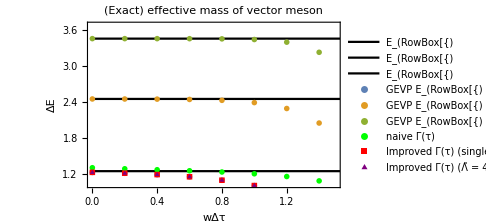

```mathematica
ClearAll[smartPlot1];
Block[{effMassE1Max, effMassE1Min, rangeE1, trange, irange},
trange = 1.5;
irange=Floor[trange/t0];
effMassE1Max=Max[Max[effMassE1M01⟦;;irange⟧], 
Max[effMassE1Op3⟦;;irange⟧], 
Max[effMassE1Op3Simple⟦;;irange⟧],  (*Max[effMassE1Op3NoisyUpper⟦;;trange⟧]],*)
Max[gapEOddP]];
effMassE1Min =gapE1;
rangeE1=effMassE1Max - effMassE1Min;
smartPlot1 = Show[gapEOddPPlot,
effMassE1Op3GEVPPrincipalsPlot,
(*}effMassE1Op3NoisyPlot,*)
effMassE1M01Plot,
effMassE1Op3SimplePlot,
effMassE1Op3Plot,
 PlotRange -> {{0, trange}, {effMassE1Min-botPaddingE1 * rangeE1,effMassE1Max+topPaddingE1* rangeE1}},
PlotLabel->Style["(Exact) effective mass of vector meson", Black, FontSize->17],
Frame->True,
FrameTicks->Automatic,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]]
```

#### smartPlot2 -- Plot with all the smart operators

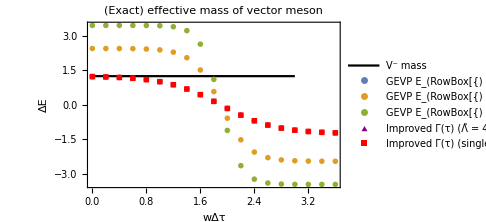

```mathematica
ClearAll[smartPlot2];
Block[{trange,effMassE1Max, effMassE1Min, rangeE1,irange},
trange = 2.0(*Floor[(T-t0)/3]*);
irange=Floor[trange/t0];
effMassE1Max=Max[Max[effMassE1Op3⟦;;irange⟧],Max[effMassE1Op3Simple⟦;;irange⟧]];(*Max[effMassE1Op3NoisyUpper⟦;;trange⟧]];*)
effMassE1Min =gapE1;
rangeE1=effMassE1Max - effMassE1Min;
smartPlot2 = Show[gapE1Plot,
effMassE1Op3GEVPPrincipalsPlot,
effMassE1Op3Plot,
effMassE1Op3SimplePlot,
 PlotRange -> {{0,trange-1}, {effMassE1Min-botPaddingE1 * rangeE1,effMassE1Max+topPaddingE1* rangeE1}},
PlotLabel->Style["(Exact) effective mass of vector meson", Black, FontSize->17],
Frame->True,
FrameTicks-> Automatic,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]
]
```

#### SmartPlot4

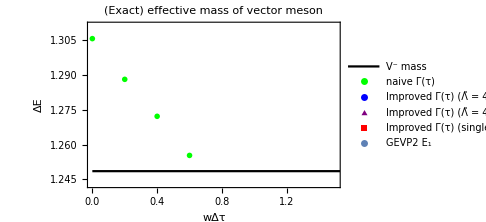

```mathematica
ClearAll[smartPlot4];
Block[{trange,irange,effMassE1Max, effMassE1Min, rangeE1},
trange = 1.5;
irange=Floor[trange/t0];
effMassE1Max=Max[effMassE1Op3⟦;;irange⟧,effMassE1Op3Simple⟦;;irange⟧,effMassE1M01⟦;;irange⟧];
effMassE1Min =gapE1;
rangeE1=effMassE1Max - effMassE1Min;
smartPlot4 = Show[gapE1Plot,
effMassE1M01Plot,
effMassE1Op3NoisyPlot,
effMassE1Op3Plot,
effMassE1Op3SimplePlot,
effMassE1Op3GEVPPrincipalsPlotTarget,
 PlotRange -> {{0,trange}, {effMassE1Min-botPaddingE1 * rangeE1,effMassE1Max+topPaddingE1* rangeE1}},
PlotLabel->Style["(Exact) effective mass of vector meson", Black, FontSize->17],
Frame->True,
FrameTicks-> Automatic,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]
]
```

#### SmartPlot5 --- Plot the “flat line” to see scale

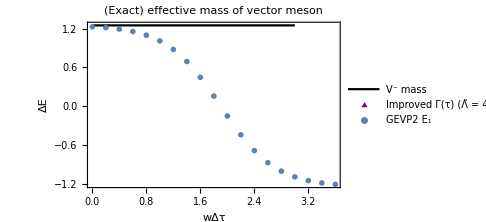

```mathematica
ClearAll[smartPlot5];
Block[{trange,irange,effMassE1Max, effMassE1Min, rangeE1},
trange = 1.5;
irange=Floor[trange/t0];
effMassE1Max=Max[Max[effMassE1Op3⟦;;irange⟧], Max[effMassE10Op3GEVPPrincipal2[1]⟦;;irange⟧]];
effMassE1Min =gapE1;
rangeE1=effMassE1Max - effMassE1Min;
smartPlot5 = Show[gapE1Plot,
effMassE1Op3Plot,
effMassE1Op3GEVPPrincipalsPlotTarget,
 PlotRange -> {{0,trange-1}, {effMassE1Min-botPaddingE1 * rangeE1,effMassE1Max+topPaddingE1* rangeE1}},
PlotLabel->Style["(Exact) effective mass of vector meson", Black, FontSize->17],
Frame->True,
FrameTicks-> Automatic,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]
]
```

```mathematica
ClearAll[smartPlot6];
Block[{effMassE1Max, effMassE1Min, rangeE1, trange, irange},
trange = 1.5;
irange=Floor[trange/t0];
effMassE1Max=Max[ Max[effMassE1Op3⟦;;irange⟧], 
Max[effMassE1Op3Simple⟦;;irange⟧],  Max[effMassE1Op3NoisyUpper⟦;;irange⟧],
Max[gapE1]];
effMassE1Min =gapE1;
rangeE1=effMassE1Max - effMassE1Min;
smartPlot6 = Show[gapE1Plot,
effMassE1Op3NoisyPlot,
effMassE1Op3SimplePlot,
effMassE1Op3Plot,
 PlotRange -> {{0, trange}, {effMassE1Min-botPaddingE1 * rangeE1,effMassE1Max+topPaddingE1* rangeE1}},
PlotLabel->Style["(Exact) effective mass of vector meson", Black, FontSize->17],
Frame->True,
FrameTicks->Automatic,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]]
```

-Graphics-

#### Save plots

```mathematica
Block[{plotName},
plotName=  conventionFileName[ToString[StringForm["smartPlot1_lmd3_`1`", Λ3]], L, Λ1, Λ2, "png"];
If[!FileExistsQ[plotName], Export[plotName, smartPlot1, ImageResolution-> imageRes]];
];
```

```mathematica
Block[{plotName},
plotName=  conventionFileName[ToString[StringForm["smartPlot2_lmd3_`1`", Λ3]], L, Λ1, Λ2, "png"];
If[!FileExistsQ[plotName], Export[plotName, smartPlot2, ImageResolution-> imageRes]];
];
```

```mathematica
Block[{plotName},
plotName=  conventionFileName[ToString[StringForm["smartPlot3_lmd3_`1`", Λ3]], L, Λ1, Λ2, "png"];
If[!FileExistsQ[plotName], Export[plotName, smartPlot3, ImageResolution-> imageRes]];
];
```

```mathematica
Block[{plotName},
plotName=  conventionFileName[ToString[StringForm["smartPlot4_lmd3_`1`", Λ3]], L, Λ1, Λ2, "png"];
If[!FileExistsQ[plotName], Export[plotName, smartPlot4, ImageResolution-> imageRes]];
];
```

```mathematica
Block[{plotName},
plotName=  conventionFileName[ToString[StringForm["smartPlot5_lmd3_`1`", Λ3]], L, Λ1, Λ2, "png"];
If[!FileExistsQ[plotName], Export[plotName, smartPlot5, ImageResolution-> imageRes]];
];
```

```mathematica
Block[{plotName},
plotName=  conventionFileName[ToString[StringForm["smartPlot6_lmd3_`1`", Λ3]], L, Λ1, Λ2, "png"];
If[!FileExistsQ[plotName], Export[plotName, smartPlot5, ImageResolution-> imageRes]];
];
```

## Debugging and Diagnostics

```mathematica
#.eOddPCoeffsCompBasis[1] & /@ {M01SnkOnGSCompBasis,op3SimpleSnkOnGSCompBasis, op3SnkOnGSCompBasis}
#.eOddPCoeffsCompBasis[1] & /@ {M01SrcOnGSCompBasis,op3SimpleSrcOnGSCompBasis,op3SrcOnGSCompBasis}
```

{-0.972765,-0.998971,0.-(1.62735 $Failed)/(√(0.+2.88815 Abs[$Failed]^2))}

{-0.718625,-0.756602,0.}

```mathematica
#.eOddPCoeffsCompBasis[2] & /@ {M01SnkOnGSCompBasis,op3SimpleSnkOnGSCompBasis, op3SnkOnGSCompBasis}
#.eOddPCoeffsCompBasis[2] & /@  {M01SrcOnGSCompBasis,op3SimpleSrcOnGSCompBasis,op3SrcOnGSCompBasis}
```

{-0.224475,-0.0452343,0.+(0.367339 $Failed)/(√(0.+2.88815 Abs[$Failed]^2))}

{-0.16583,-0.0342596,0.}

```mathematica
#.eOddPCoeffsCompBasis[3] & /@ {M01SnkOnGSCompBasis,op3SimpleSnkOnGSCompBasis, op3SnkOnGSCompBasis}
#.eOddPCoeffsCompBasis[3] & /@ {M01SrcOnGSCompBasis,op3SimpleSrcOnGSCompBasis,op3SrcOnGSCompBasis}
```

{0.0318501,-0.0028929,0.+(0.304713 $Failed)/(√(0.+2.88815 Abs[$Failed]^2))}

{0.0235291,-0.00219103,0.}

```mathematica
#.eOddPCoeffsCompBasis[4] & /@  {M01SnkOnGSCompBasis,op3SimpleSnkOnGSCompBasis, op3SnkOnGSCompBasis}
#.eOddPCoeffsCompBasis[4] & /@ {M01SrcOnGSCompBasis,op3SimpleSrcOnGSCompBasis,op3SrcOnGSCompBasis}
```

{0.048207,0.00120251,0.+(0.109921 $Failed)/(√(0.+2.88815 Abs[$Failed]^2))}

{0.0356126,0.000910758,0.}